```mathematica
Clear[ϕ,ΔA,ΔB,AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,AαiH,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi={{d11 Exp[I ψ11],d12 Exp[I ψ12],d13 Exp[I ψ13]},{d21 Exp[I ψ21],d22 Exp[I ψ22],d23 Exp[I ψ23]},{d31 Exp[I ψ31],d32 Exp[I ψ32],d33 Exp[I ψ33]}};
(* Dαi in polar repps *)
Print[Style[" Dαi looks like : ",Red,16]]
Dαi//MatrixForm
Print[Style[" Trace of Dαi is : ",16,Red]]
FullSimplify[Tr[Dαi.ConjugateTranspose[Dαi]],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals}]
Aαi=AαiA+ϕ Dαi;
(**********************************)
(*AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals,{D11,D12,D13,D21,D22,D23,D31,D32,D33}∈Reals,ΔA>0,ΔB>0}];*)
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0}];
(**********************************)
Print[Style[" α Aαi Aαi^* term:",Red,16]]
(*fα=Simplify[α Tr[Aαi.AαiH],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals,{D11,D12,D13,D21,D22,D23,D31,D32,D33}∈Reals,ΔA>0,ΔB>0}]*)
fα=Simplify[α Tr[Aαi.AαiH],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
fαϕ=Collect[%,ϕ]
```

Dαi looks like :

(d11 ⅇ^(ⅈ ψ11) | d12 ⅇ^(ⅈ ψ12) | d13 ⅇ^(ⅈ ψ13)
d21 ⅇ^(ⅈ ψ21) | d22 ⅇ^(ⅈ ψ22) | d23 ⅇ^(ⅈ ψ23)
d31 ⅇ^(ⅈ ψ31) | d32 ⅇ^(ⅈ ψ32) | d33 ⅇ^(ⅈ ψ33))

Trace of Dαi is :

d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2

α Aαi Aαi^* term:

α ΔA^2+(ⅇ^(-ⅈ (ψ11+ψ12)) (d11 ⅇ^(ⅈ ψ12) (1+ⅇ^(2 ⅈ ψ11))-ⅈ d12 ⅇ^(ⅈ ψ11) (-1+ⅇ^(2 ⅈ ψ12))) α ΔA ϕ)/(√2)+α ϕ^2

```mathematica
Clear[ϕ,ΔA,ΔB,AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,AαiH,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi={{d11 Exp[I ψ11],d12 Exp[I ψ12],d13 Exp[I ψ13]},{d21 Exp[I ψ21],d22 Exp[I ψ22],d23 Exp[I ψ23]},{d31 Exp[I ψ31],d32 Exp[I ψ32],d33 Exp[I ψ33]}};
Aαi=AαiA+ϕ Dαi;
(**********************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
(*AαiC=Conjugate[Aαi];
AαiH=ConjugateTranspose[Aαi];
AαiT=Transpose[Aαi];*)
(**********************************)
Print[Style[" β1 Aαi^* Aαi^* Aβj Aβj term:",Red,16]]
fβ1=Simplify[β1 (Tr[AαiC.AαiH]) (Tr[Aαi.AαiT]),Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
fβ1ϕ=Collect[%,ϕ]
```

β1 Aαi^* Aαi^* Aβj Aβj term:

β1 (2 d11^2 ΔA^2+2 d12^2 ΔA^2-2 ⅈ d11 d12 ⅇ^(ⅈ ψ11-ⅈ ψ12) ΔA^2+2 ⅈ d11 d12 ⅇ^(-ⅈ ψ11+ⅈ ψ12) ΔA^2) ϕ^2+β1 (√2 d11^3 ⅇ^(-ⅈ ψ11) ΔA+√2 d11^3 ⅇ^(ⅈ ψ11) ΔA-ⅈ √2 d11^2 d12 ⅇ^(2 ⅈ ψ11-ⅈ ψ12) ΔA+ⅈ √2 d11^2 d12 ⅇ^(-2 ⅈ ψ11+ⅈ ψ12) ΔA+√2 d11 d12^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ12) ΔA+√2 d11 d12^2 ⅇ^(-ⅈ ψ11+2 ⅈ ψ12) ΔA+ⅈ √2 d12^3 ⅇ^(-ⅈ ψ12) ΔA-ⅈ √2 d12^3 ⅇ^(ⅈ ψ12) ΔA+√2 d11 d13^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ13) ΔA+ⅈ √2 d12 d13^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ13) ΔA+√2 d11 d21^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ21) ΔA+ⅈ √2 d12 d21^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ21) ΔA+√2 d11 d22^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ22) ΔA+ⅈ √2 d12 d22^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ22) ΔA+√2 d11 d23^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ23) ΔA+ⅈ √2 d12 d23^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ23) ΔA+√2 d11 d31^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ31) ΔA+ⅈ √2 d12 d31^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ31) ΔA+√2 d11 d32^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ32) ΔA+ⅈ √2 d12 d32^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ32) ΔA+√2 d11 d33^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ33) ΔA+ⅈ √2 d12 d33^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ33) ΔA+√2 d11 ⅇ^(-ⅈ ψ11) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33)) ΔA-ⅈ √2 d12 ⅇ^(-ⅈ ψ12) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33)) ΔA) ϕ^3+(d11^4+d12^4+d11^2 d12^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ12)+d11^2 d12^2 ⅇ^(-2 ⅈ ψ11+2 ⅈ ψ12)+d11^2 d13^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ13)+d12^2 d13^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ13)+d11^2 d21^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ21)+d12^2 d21^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ21)+d11^2 d22^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ22)+d12^2 d22^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ22)+d11^2 d23^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ23)+d12^2 d23^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ23)+d11^2 d31^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ31)+d12^2 d31^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ31)+d11^2 d32^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ32)+d12^2 d32^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ32)+d11^2 d33^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ33)+d12^2 d33^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ33)+d11^2 ⅇ^(-2 ⅈ ψ11) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d12^2 ⅇ^(-2 ⅈ ψ12) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d13^2 ⅇ^(-2 ⅈ ψ13) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d21^2 ⅇ^(-2 ⅈ ψ21) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d22^2 ⅇ^(-2 ⅈ ψ22) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d23^2 ⅇ^(-2 ⅈ ψ23) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d31^2 ⅇ^(-2 ⅈ ψ31) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d32^2 ⅇ^(-2 ⅈ ψ32) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d33^2 ⅇ^(-2 ⅈ ψ33) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))) β1 ϕ^4

```mathematica
Clear[ϕ,ΔA,ΔB,AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,AαiH,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi={{d11 Exp[I ψ11],d12 Exp[I ψ12],d13 Exp[I ψ13]},{d21 Exp[I ψ21],d22 Exp[I ψ22],d23 Exp[I ψ23]},{d31 Exp[I ψ31],d32 Exp[I ψ32],d33 Exp[I ψ33]}};
Aαi=AαiA+ϕ Dαi;
(*****************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
(*****************************************)
Print[Style[" β2 Aαi^* Aαi Aβj^* Aβj term:",Red,16]]
fβ2=FullSimplify[β2 (Tr[AαiC.AαiT]) (Tr[AαiC.AαiT]),Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
fβ2ϕ=Collect[%,ϕ]
```

β2 Aαi^* Aαi Aβj^* Aβj term:

β2 ΔA^4+β2 ϕ^4+2 √2 β2 ΔA^3 ϕ (d11 Cos[ψ11]+d12 Sin[ψ12])+2 √2 β2 ΔA ϕ^3 (d11 Cos[ψ11]+d12 Sin[ψ12])+β2 ϕ^2 (2 ΔA^2+2 ΔA^2 (d11 Cos[ψ11]+d12 Sin[ψ12])^2)

```mathematica
Clear[ϕ,ΔA,ΔB,AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,AαiH,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi={{d11 Exp[I ψ11],d12 Exp[I ψ12],d13 Exp[I ψ13]},{d21 Exp[I ψ21],d22 Exp[I ψ22],d23 Exp[I ψ23]},{d31 Exp[I ψ31],d32 Exp[I ψ32],d33 Exp[I ψ33]}};
Aαi=AαiA+ϕ Dαi;
(*****************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
(*****************************************)
Print[Style[" β3 Aαi^* Aβi^* Aαj Aβj term:",Red,16]]
fβ3=FullSimplify[β3 Tr[(AαiC.AαiH).((Aαi.AαiT)ᵀ)],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
fβ3ϕ=Collect[%,ϕ]
```

β3 Aαi^* Aβi^* Aαj Aβj term:

β3 ϕ^4 ((d11^2+d21^2+d31^2)^2+(d12^2+d22^2+d32^2)^2+(d13^2+d23^2+d33^2)^2+2 d21^2 d22^2 Cos[2 ψ21-2 ψ22]+2 d31^2 d32^2 Cos[2 ψ31-2 ψ32]+2 (d11^2 d12^2 Cos[2 ψ11-2 ψ12]+d11^2 d13^2 Cos[2 ψ11-2 ψ13]+d12^2 d13^2 Cos[2 ψ12-2 ψ13]+2 d11 d12 d21 d22 Cos[ψ11-ψ12+ψ21-ψ22]+d21^2 d23^2 Cos[2 ψ21-2 ψ23]+d22^2 d23^2 Cos[2 ψ22-2 ψ23]+2 d11 d13 d21 d23 Cos[ψ11-ψ13+ψ21-ψ23]+2 d12 d13 d22 d23 Cos[ψ12-ψ13+ψ22-ψ23]+2 d11 d12 d31 d32 Cos[ψ11-ψ12+ψ31-ψ32]+2 d21 d22 d31 d32 Cos[ψ21-ψ22+ψ31-ψ32]+d31^2 d33^2 Cos[2 ψ31-2 ψ33]+d32^2 d33^2 Cos[2 ψ32-2 ψ33]+2 d11 d13 d31 d33 Cos[ψ11-ψ13+ψ31-ψ33]+2 d21 d23 d31 d33 Cos[ψ21-ψ23+ψ31-ψ33]+2 d12 d13 d32 d33 Cos[ψ12-ψ13+ψ32-ψ33]+2 d22 d23 d32 d33 Cos[ψ22-ψ23+ψ32-ψ33]))+β3 ΔA^2 ϕ^2 (2 d11^2+2 d12^2+d21^2+d22^2+d31^2+d32^2+4 d11 d12 Sin[ψ11-ψ12]+2 d21 d22 Sin[ψ21-ψ22]+2 d31 d32 Sin[ψ31-ψ32])+2 √2 β3 ΔA ϕ^3 (d11 (d11^2+d21^2+d31^2) Cos[ψ11]+d11 d12^2 Cos[ψ11-2 ψ12]+d11 d13^2 Cos[ψ11-2 ψ13]+d12 d21 d22 Cos[ψ12-ψ21+ψ22]+d13 d21 d23 Cos[ψ13-ψ21+ψ23]+d12 d31 d32 Cos[ψ12-ψ31+ψ32]+d13 d31 d33 Cos[ψ13-ψ31+ψ33]+d11^2 d12 Sin[2 ψ11-ψ12]+d12^3 Sin[ψ12]+d12 d22^2 Sin[ψ12]+d12 d32^2 Sin[ψ12]-d12 d13^2 Sin[ψ12-2 ψ13]+d11 d21 d22 Sin[ψ11+ψ21-ψ22]+d13 d22 d23 Sin[ψ13-ψ22+ψ23]+d11 d31 d32 Sin[ψ11+ψ31-ψ32]+d13 d32 d33 Sin[ψ13-ψ32+ψ33])

```mathematica
Clear[ϕ,ΔA,ΔB,AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,AαiH,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi={{d11 Exp[I ψ11],d12 Exp[I ψ12],d13 Exp[I ψ13]},{d21 Exp[I ψ21],d22 Exp[I ψ22],d23 Exp[I ψ23]},{d31 Exp[I ψ31],d32 Exp[I ψ32],d33 Exp[I ψ33]}};
Aαi=AαiA+ϕ Dαi;
(*****************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
(*****************************************)
Print[Style[" β4 Aαi^* Aβi Aβj^* Aαj term:",Red,16]]
fβ4=FullSimplify[β4 Tr[(AαiC.AαiT).(AαiC.AαiT)],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
fβ4ϕ=Collect[fβ4,ϕ]
```

β4 Aαi^* Aβi Aβj^* Aαj term:

β4 ΔA^4+β4 ϕ^4 ((d11^2+d12^2+d13^2)^2+2 d11^2 d21^2+2 d12^2 d22^2+2 d13^2 d23^2+(d21^2+d22^2+d23^2)^2+2 d11^2 d31^2+2 d12^2 d32^2+2 d13^2 d33^2+(d31^2+d32^2+d33^2)^2+2 d11 d12 d21 d22 ⅇ^(-ⅈ ψ11+ⅈ ψ12+ⅈ ψ21-ⅈ ψ22)+2 d11 d12 d21 d22 ⅇ^(ⅈ ψ11-ⅈ ψ12-ⅈ ψ21+ⅈ ψ22)+2 d11 d13 d21 d23 ⅇ^(ⅈ ψ11-ⅈ ψ21-ⅈ (ψ13-ψ23))+2 d12 d13 d22 d23 ⅇ^(ⅈ ψ12-ⅈ ψ22-ⅈ (ψ13-ψ23))+2 d11 d13 d21 d23 ⅇ^(-ⅈ ψ11+ⅈ ψ21+ⅈ (ψ13-ψ23))+2 d12 d13 d22 d23 ⅇ^(-ⅈ ψ12+ⅈ ψ22+ⅈ (ψ13-ψ23))+2 d11 d12 d31 d32 ⅇ^(-ⅈ ψ11+ⅈ ψ12+ⅈ ψ31-ⅈ ψ32)+2 d11 d12 d31 d32 ⅇ^(ⅈ ψ11-ⅈ ψ12-ⅈ ψ31+ⅈ ψ32)+2 d11 d13 d31 d33 ⅇ^(ⅈ ψ11-ⅈ ψ31-ⅈ (ψ13-ψ33))+2 d12 d13 d32 d33 ⅇ^(ⅈ ψ12-ⅈ ψ32-ⅈ (ψ13-ψ33))+2 d11 d13 d31 d33 ⅇ^(-ⅈ ψ11+ⅈ ψ31+ⅈ (ψ13-ψ33))+2 d12 d13 d32 d33 ⅇ^(-ⅈ ψ12+ⅈ ψ32+ⅈ (ψ13-ψ33))+2 (d21^2 d31^2+d22^2 d32^2+d23^2 d33^2+2 d21 d22 d31 d32 Cos[ψ21-ψ22-ψ31+ψ32]+2 d23 d33 (d21 d31 Cos[ψ21-ψ23-ψ31+ψ33]+d22 d32 Cos[ψ22-ψ23-ψ32+ψ33])))+2 √2 β4 ΔA^3 ϕ (d11 Cos[ψ11]+d12 Sin[ψ12])+β4 ϕ^3 (√2 d11 d21^2 ⅇ^(-ⅈ ψ11) ΔA+√2 d11 d31^2 ⅇ^(-ⅈ ψ11) ΔA+√2 d11 d21^2 ⅇ^(ⅈ ψ11) ΔA+√2 d11 d31^2 ⅇ^(ⅈ ψ11) ΔA+ⅈ √2 d12 d22^2 ⅇ^(-ⅈ ψ12) ΔA+ⅈ √2 d12 d32^2 ⅇ^(-ⅈ ψ12) ΔA-ⅈ √2 d12 d22^2 ⅇ^(ⅈ ψ12) ΔA-ⅈ √2 d12 d32^2 ⅇ^(ⅈ ψ12) ΔA+ⅈ √2 d11 d21 d22 ⅇ^(-ⅈ ψ11+ⅈ ψ21-ⅈ ψ22) ΔA+√2 d12 d21 d22 ⅇ^(ⅈ ψ12+ⅈ ψ21-ⅈ ψ22) ΔA-ⅈ √2 d11 d21 d22 ⅇ^(ⅈ ψ11-ⅈ ψ21+ⅈ ψ22) ΔA+√2 d12 d21 d22 ⅇ^(-ⅈ ψ12-ⅈ ψ21+ⅈ ψ22) ΔA+√2 d13 d21 d23 ⅇ^(-ⅈ ψ21-ⅈ (ψ13-ψ23)) ΔA+ⅈ √2 d13 d22 d23 ⅇ^(-ⅈ ψ22-ⅈ (ψ13-ψ23)) ΔA+√2 d13 d21 d23 ⅇ^(ⅈ ψ21+ⅈ (ψ13-ψ23)) ΔA-ⅈ √2 d13 d22 d23 ⅇ^(ⅈ ψ22+ⅈ (ψ13-ψ23)) ΔA+ⅈ √2 d11 d31 d32 ⅇ^(-ⅈ ψ11+ⅈ ψ31-ⅈ ψ32) ΔA+√2 d12 d31 d32 ⅇ^(ⅈ ψ12+ⅈ ψ31-ⅈ ψ32) ΔA-ⅈ √2 d11 d31 d32 ⅇ^(ⅈ ψ11-ⅈ ψ31+ⅈ ψ32) ΔA+√2 d12 d31 d32 ⅇ^(-ⅈ ψ12-ⅈ ψ31+ⅈ ψ32) ΔA+√2 d13 d31 d33 ⅇ^(-ⅈ ψ31-ⅈ (ψ13-ψ33)) ΔA+ⅈ √2 d13 d32 d33 ⅇ^(-ⅈ ψ32-ⅈ (ψ13-ψ33)) ΔA+√2 d13 d31 d33 ⅇ^(ⅈ ψ31+ⅈ (ψ13-ψ33)) ΔA-ⅈ √2 d13 d32 d33 ⅇ^(ⅈ ψ32+ⅈ (ψ13-ψ33)) ΔA+2 √2 (d11^2+d12^2+d13^2) ΔA (d11 Cos[ψ11]+d12 Sin[ψ12]))+β4 ϕ^2 (2 (d11^2+d12^2+d13^2) ΔA^2+d21^2 ΔA^2+d22^2 ΔA^2+d31^2 ΔA^2+d32^2 ΔA^2+ⅈ d21 d22 ⅇ^(ⅈ ψ21-ⅈ ψ22) ΔA^2-ⅈ d21 d22 ⅇ^(-ⅈ ψ21+ⅈ ψ22) ΔA^2+ⅈ d31 d32 ⅇ^(ⅈ ψ31-ⅈ ψ32) ΔA^2-ⅈ d31 d32 ⅇ^(-ⅈ ψ31+ⅈ ψ32) ΔA^2+2 ΔA^2 (d11 Cos[ψ11]+d12 Sin[ψ12])^2)

```mathematica
Clear[ϕ,ΔA,ΔB,AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,AαiH,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi={{d11 Exp[I ψ11],d12 Exp[I ψ12],d13 Exp[I ψ13]},{d21 Exp[I ψ21],d22 Exp[I ψ22],d23 Exp[I ψ23]},{d31 Exp[I ψ31],d32 Exp[I ψ32],d33 Exp[I ψ33]}};
Print[Style[" Dαi looks like : ",16,Red]]
Dαi//MatrixForm
Aαi=AαiA+ϕ Dαi;
(***************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
(***************************************)
Print[Style[" β5 Aαi^* Aβi Aβj Aαj^* term:",Red,16]]
fβ5=FullSimplify[β5 Tr[(AαiC.AαiT).(Aαi.AαiH)],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}];
fβ5ϕ=Collect[fβ5,ϕ]
```

Dαi looks like :

(d11 ⅇ^(ⅈ ψ11) | d12 ⅇ^(ⅈ ψ12) | d13 ⅇ^(ⅈ ψ13)
d21 ⅇ^(ⅈ ψ21) | d22 ⅇ^(ⅈ ψ22) | d23 ⅇ^(ⅈ ψ23)
d31 ⅇ^(ⅈ ψ31) | d32 ⅇ^(ⅈ ψ32) | d33 ⅇ^(ⅈ ψ33))

β5 Aαi^* Aβi Aβj Aαj^* term:

β5 ΔA^4+((d11^2+d12^2+d13^2)^2+(d21^2+d22^2+d23^2)^2+(d31^2+d32^2+d33^2)^2+d11^2 d21^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ21)+d11^2 d21^2 ⅇ^(-2 ⅈ ψ11+2 ⅈ ψ21)+2 d11 d12 d21 d22 ⅇ^(ⅈ ψ11+ⅈ ψ12-ⅈ ψ21-ⅈ ψ22)+2 d11 d12 d21 d22 ⅇ^(-ⅈ ψ11-ⅈ ψ12+ⅈ ψ21+ⅈ ψ22)+d12^2 d22^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ22)+d12^2 d22^2 ⅇ^(-2 ⅈ ψ12+2 ⅈ ψ22)+2 d11 d13 d21 d23 ⅇ^(-ⅈ ψ11+ⅈ ψ21-ⅈ (ψ13-ψ23))+2 d12 d13 d22 d23 ⅇ^(-ⅈ ψ12+ⅈ ψ22-ⅈ (ψ13-ψ23))+2 d11 d13 d21 d23 ⅇ^(ⅈ ψ11-ⅈ ψ21+ⅈ (ψ13-ψ23))+2 d12 d13 d22 d23 ⅇ^(ⅈ ψ12-ⅈ ψ22+ⅈ (ψ13-ψ23))+d13^2 d23^2 ⅇ^(-2 ⅈ (ψ13-ψ23))+d13^2 d23^2 ⅇ^(2 ⅈ (ψ13-ψ23))+d11^2 d31^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ31)+d11^2 d31^2 ⅇ^(-2 ⅈ ψ11+2 ⅈ ψ31)+2 d11 d12 d31 d32 ⅇ^(ⅈ ψ11+ⅈ ψ12-ⅈ ψ31-ⅈ ψ32)+2 d11 d12 d31 d32 ⅇ^(-ⅈ ψ11-ⅈ ψ12+ⅈ ψ31+ⅈ ψ32)+d12^2 d32^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ32)+d12^2 d32^2 ⅇ^(-2 ⅈ ψ12+2 ⅈ ψ32)+2 d11 d13 d31 d33 ⅇ^(-ⅈ ψ11+ⅈ ψ31-ⅈ (ψ13-ψ33))+2 d12 d13 d32 d33 ⅇ^(-ⅈ ψ12+ⅈ ψ32-ⅈ (ψ13-ψ33))+2 d11 d13 d31 d33 ⅇ^(ⅈ ψ11-ⅈ ψ31+ⅈ (ψ13-ψ33))+2 d12 d13 d32 d33 ⅇ^(ⅈ ψ12-ⅈ ψ32+ⅈ (ψ13-ψ33))+d13^2 d33^2 ⅇ^(-2 ⅈ (ψ13-ψ33))+d13^2 d33^2 ⅇ^(2 ⅈ (ψ13-ψ33))+ⅇ^(-2 ⅈ (ψ21+ψ22+ψ23)) (d21 d31 ⅇ^(ⅈ (ψ22+ψ23+ψ31))+d22 d32 ⅇ^(ⅈ (ψ21+ψ23+ψ32))+d23 d33 ⅇ^(ⅈ (ψ21+ψ22+ψ33)))^2+ⅇ^(-2 ⅈ (ψ31+ψ32+ψ33)) (d23 d33 ⅇ^(ⅈ (ψ23+ψ31+ψ32))+d22 d32 ⅇ^(ⅈ (ψ22+ψ31+ψ33))+d21 d31 ⅇ^(ⅈ (ψ21+ψ32+ψ33)))^2) β5 ϕ^4+2 √2 β5 ΔA^3 ϕ (d11 Cos[ψ11]+d12 Sin[ψ12])+β5 ϕ^3 (√2 d11 d21^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ21) ΔA+√2 d11 d21^2 ⅇ^(-ⅈ ψ11+2 ⅈ ψ21) ΔA+ⅈ √2 d11 d21 d22 ⅇ^(ⅈ ψ11-ⅈ ψ21-ⅈ ψ22) ΔA+√2 d12 d21 d22 ⅇ^(ⅈ ψ12-ⅈ ψ21-ⅈ ψ22) ΔA-ⅈ √2 d11 d21 d22 ⅇ^(-ⅈ ψ11+ⅈ ψ21+ⅈ ψ22) ΔA+√2 d12 d21 d22 ⅇ^(-ⅈ ψ12+ⅈ ψ21+ⅈ ψ22) ΔA+ⅈ √2 d12 d22^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ22) ΔA-ⅈ √2 d12 d22^2 ⅇ^(-ⅈ ψ12+2 ⅈ ψ22) ΔA+√2 d13 d21 d23 ⅇ^(ⅈ ψ21-ⅈ (ψ13-ψ23)) ΔA-ⅈ √2 d13 d22 d23 ⅇ^(ⅈ ψ22-ⅈ (ψ13-ψ23)) ΔA+√2 d13 d21 d23 ⅇ^(-ⅈ ψ21+ⅈ (ψ13-ψ23)) ΔA+ⅈ √2 d13 d22 d23 ⅇ^(-ⅈ ψ22+ⅈ (ψ13-ψ23)) ΔA+√2 d11 d31^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ31) ΔA+√2 d11 d31^2 ⅇ^(-ⅈ ψ11+2 ⅈ ψ31) ΔA+ⅈ √2 d11 d31 d32 ⅇ^(ⅈ ψ11-ⅈ ψ31-ⅈ ψ32) ΔA+√2 d12 d31 d32 ⅇ^(ⅈ ψ12-ⅈ ψ31-ⅈ ψ32) ΔA-ⅈ √2 d11 d31 d32 ⅇ^(-ⅈ ψ11+ⅈ ψ31+ⅈ ψ32) ΔA+√2 d12 d31 d32 ⅇ^(-ⅈ ψ12+ⅈ ψ31+ⅈ ψ32) ΔA+ⅈ √2 d12 d32^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ32) ΔA-ⅈ √2 d12 d32^2 ⅇ^(-ⅈ ψ12+2 ⅈ ψ32) ΔA+√2 d13 d31 d33 ⅇ^(ⅈ ψ31-ⅈ (ψ13-ψ33)) ΔA-ⅈ √2 d13 d32 d33 ⅇ^(ⅈ ψ32-ⅈ (ψ13-ψ33)) ΔA+√2 d13 d31 d33 ⅇ^(-ⅈ ψ31+ⅈ (ψ13-ψ33)) ΔA+ⅈ √2 d13 d32 d33 ⅇ^(-ⅈ ψ32+ⅈ (ψ13-ψ33)) ΔA+2 √2 (d11^2+d12^2+d13^2) ΔA (d11 Cos[ψ11]+d12 Sin[ψ12]))+β5 ϕ^2 (2 (d11^2+d12^2+d13^2) ΔA^2+1/2 d21^2 ⅇ^(-2 ⅈ ψ21) ΔA^2+1/2 d21^2 ⅇ^(2 ⅈ ψ21) ΔA^2+ⅈ d21 d22 ⅇ^(-ⅈ ψ21-ⅈ ψ22) ΔA^2-ⅈ d21 d22 ⅇ^(ⅈ ψ21+ⅈ ψ22) ΔA^2-1/2 d22^2 ⅇ^(-2 ⅈ ψ22) ΔA^2-1/2 d22^2 ⅇ^(2 ⅈ ψ22) ΔA^2+1/2 d31^2 ⅇ^(-2 ⅈ ψ31) ΔA^2+1/2 d31^2 ⅇ^(2 ⅈ ψ31) ΔA^2+ⅈ d31 d32 ⅇ^(-ⅈ ψ31-ⅈ ψ32) ΔA^2-ⅈ d31 d32 ⅇ^(ⅈ ψ31+ⅈ ψ32) ΔA^2-1/2 d32^2 ⅇ^(-2 ⅈ ψ32) ΔA^2-1/2 d32^2 ⅇ^(2 ⅈ ψ32) ΔA^2+2 ΔA^2 (d11 Cos[ψ11]+d12 Sin[ψ12])^2)

```mathematica
Clear[CoefficientOfϕ,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33,ΔA,ΔB,β1,β2,β3,β4,β5,α];
fϕ=Collect[(fα+fβ1ϕ+fβ2ϕ+fβ3ϕ+fβ4ϕ+fβ5ϕ),ϕ]-(α ΔA^2+β2 ΔA^4+β4 ΔA^4+β5 ΔA^4)
Level[fϕ,1]
```

ϕ^4 ((d11^4+d12^4+d11^2 d12^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ12)+d11^2 d12^2 ⅇ^(-2 ⅈ ψ11+2 ⅈ ψ12)+d11^2 d13^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ13)+d12^2 d13^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ13)+d11^2 d21^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ21)+d12^2 d21^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ21)+d11^2 d22^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ22)+d12^2 d22^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ22)+d11^2 d23^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ23)+d12^2 d23^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ23)+d11^2 d31^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ31)+d12^2 d31^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ31)+d11^2 d32^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ32)+d12^2 d32^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ32)+d11^2 d33^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ33)+d12^2 d33^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ33)+d11^2 ⅇ^(-2 ⅈ ψ11) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d12^2 ⅇ^(-2 ⅈ ψ12) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d13^2 ⅇ^(-2 ⅈ ψ13) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d21^2 ⅇ^(-2 ⅈ ψ21) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d22^2 ⅇ^(-2 ⅈ ψ22) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d23^2 ⅇ^(-2 ⅈ ψ23) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d31^2 ⅇ^(-2 ⅈ ψ31) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d32^2 ⅇ^(-2 ⅈ ψ32) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d33^2 ⅇ^(-2 ⅈ ψ33) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))) β1+β2+((d11^2+d12^2+d13^2)^2+(d21^2+d22^2+d23^2)^2+(d31^2+d32^2+d33^2)^2+d11^2 d21^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ21)+d11^2 d21^2 ⅇ^(-2 ⅈ ψ11+2 ⅈ ψ21)+2 d11 d12 d21 d22 ⅇ^(ⅈ ψ11+ⅈ ψ12-ⅈ ψ21-ⅈ ψ22)+2 d11 d12 d21 d22 ⅇ^(-ⅈ ψ11-ⅈ ψ12+ⅈ ψ21+ⅈ ψ22)+d12^2 d22^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ22)+d12^2 d22^2 ⅇ^(-2 ⅈ ψ12+2 ⅈ ψ22)+2 d11 d13 d21 d23 ⅇ^(-ⅈ ψ11+ⅈ ψ21-ⅈ (ψ13-ψ23))+2 d12 d13 d22 d23 ⅇ^(-ⅈ ψ12+ⅈ ψ22-ⅈ (ψ13-ψ23))+2 d11 d13 d21 d23 ⅇ^(ⅈ ψ11-ⅈ ψ21+ⅈ (ψ13-ψ23))+2 d12 d13 d22 d23 ⅇ^(ⅈ ψ12-ⅈ ψ22+ⅈ (ψ13-ψ23))+d13^2 d23^2 ⅇ^(-2 ⅈ (ψ13-ψ23))+d13^2 d23^2 ⅇ^(2 ⅈ (ψ13-ψ23))+d11^2 d31^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ31)+d11^2 d31^2 ⅇ^(-2 ⅈ ψ11+2 ⅈ ψ31)+2 d11 d12 d31 d32 ⅇ^(ⅈ ψ11+ⅈ ψ12-ⅈ ψ31-ⅈ ψ32)+2 d11 d12 d31 d32 ⅇ^(-ⅈ ψ11-ⅈ ψ12+ⅈ ψ31+ⅈ ψ32)+d12^2 d32^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ32)+d12^2 d32^2 ⅇ^(-2 ⅈ ψ12+2 ⅈ ψ32)+2 d11 d13 d31 d33 ⅇ^(-ⅈ ψ11+ⅈ ψ31-ⅈ (ψ13-ψ33))+2 d12 d13 d32 d33 ⅇ^(-ⅈ ψ12+ⅈ ψ32-ⅈ (ψ13-ψ33))+2 d11 d13 d31 d33 ⅇ^(ⅈ ψ11-ⅈ ψ31+ⅈ (ψ13-ψ33))+2 d12 d13 d32 d33 ⅇ^(ⅈ ψ12-ⅈ ψ32+ⅈ (ψ13-ψ33))+d13^2 d33^2 ⅇ^(-2 ⅈ (ψ13-ψ33))+d13^2 d33^2 ⅇ^(2 ⅈ (ψ13-ψ33))+ⅇ^(-2 ⅈ (ψ21+ψ22+ψ23)) (d21 d31 ⅇ^(ⅈ (ψ22+ψ23+ψ31))+d22 d32 ⅇ^(ⅈ (ψ21+ψ23+ψ32))+d23 d33 ⅇ^(ⅈ (ψ21+ψ22+ψ33)))^2+ⅇ^(-2 ⅈ (ψ31+ψ32+ψ33)) (d23 d33 ⅇ^(ⅈ (ψ23+ψ31+ψ32))+d22 d32 ⅇ^(ⅈ (ψ22+ψ31+ψ33))+d21 d31 ⅇ^(ⅈ (ψ21+ψ32+ψ33)))^2) β5+β3 ((d11^2+d21^2+d31^2)^2+(d12^2+d22^2+d32^2)^2+(d13^2+d23^2+d33^2)^2+2 d21^2 d22^2 Cos[2 ψ21-2 ψ22]+2 d31^2 d32^2 Cos[2 ψ31-2 ψ32]+2 (d11^2 d12^2 Cos[2 ψ11-2 ψ12]+d11^2 d13^2 Cos[2 ψ11-2 ψ13]+d12^2 d13^2 Cos[2 ψ12-2 ψ13]+2 d11 d12 d21 d22 Cos[ψ11-ψ12+ψ21-ψ22]+d21^2 d23^2 Cos[2 ψ21-2 ψ23]+d22^2 d23^2 Cos[2 ψ22-2 ψ23]+2 d11 d13 d21 d23 Cos[ψ11-ψ13+ψ21-ψ23]+2 d12 d13 d22 d23 Cos[ψ12-ψ13+ψ22-ψ23]+2 d11 d12 d31 d32 Cos[ψ11-ψ12+ψ31-ψ32]+2 d21 d22 d31 d32 Cos[ψ21-ψ22+ψ31-ψ32]+d31^2 d33^2 Cos[2 ψ31-2 ψ33]+d32^2 d33^2 Cos[2 ψ32-2 ψ33]+2 d11 d13 d31 d33 Cos[ψ11-ψ13+ψ31-ψ33]+2 d21 d23 d31 d33 Cos[ψ21-ψ23+ψ31-ψ33]+2 d12 d13 d32 d33 Cos[ψ12-ψ13+ψ32-ψ33]+2 d22 d23 d32 d33 Cos[ψ22-ψ23+ψ32-ψ33]))+β4 ((d11^2+d12^2+d13^2)^2+2 d11^2 d21^2+2 d12^2 d22^2+2 d13^2 d23^2+(d21^2+d22^2+d23^2)^2+2 d11^2 d31^2+2 d12^2 d32^2+2 d13^2 d33^2+(d31^2+d32^2+d33^2)^2+2 d11 d12 d21 d22 ⅇ^(-ⅈ ψ11+ⅈ ψ12+ⅈ ψ21-ⅈ ψ22)+2 d11 d12 d21 d22 ⅇ^(ⅈ ψ11-ⅈ ψ12-ⅈ ψ21+ⅈ ψ22)+2 d11 d13 d21 d23 ⅇ^(ⅈ ψ11-ⅈ ψ21-ⅈ (ψ13-ψ23))+2 d12 d13 d22 d23 ⅇ^(ⅈ ψ12-ⅈ ψ22-ⅈ (ψ13-ψ23))+2 d11 d13 d21 d23 ⅇ^(-ⅈ ψ11+ⅈ ψ21+ⅈ (ψ13-ψ23))+2 d12 d13 d22 d23 ⅇ^(-ⅈ ψ12+ⅈ ψ22+ⅈ (ψ13-ψ23))+2 d11 d12 d31 d32 ⅇ^(-ⅈ ψ11+ⅈ ψ12+ⅈ ψ31-ⅈ ψ32)+2 d11 d12 d31 d32 ⅇ^(ⅈ ψ11-ⅈ ψ12-ⅈ ψ31+ⅈ ψ32)+2 d11 d13 d31 d33 ⅇ^(ⅈ ψ11-ⅈ ψ31-ⅈ (ψ13-ψ33))+2 d12 d13 d32 d33 ⅇ^(ⅈ ψ12-ⅈ ψ32-ⅈ (ψ13-ψ33))+2 d11 d13 d31 d33 ⅇ^(-ⅈ ψ11+ⅈ ψ31+ⅈ (ψ13-ψ33))+2 d12 d13 d32 d33 ⅇ^(-ⅈ ψ12+ⅈ ψ32+ⅈ (ψ13-ψ33))+2 (d21^2 d31^2+d22^2 d32^2+d23^2 d33^2+2 d21 d22 d31 d32 Cos[ψ21-ψ22-ψ31+ψ32]+2 d23 d33 (d21 d31 Cos[ψ21-ψ23-ψ31+ψ33]+d22 d32 Cos[ψ22-ψ23-ψ32+ψ33]))))+ϕ ((ⅇ^(-ⅈ (ψ11+ψ12)) (d11 ⅇ^(ⅈ ψ12) (1+ⅇ^(2 ⅈ ψ11))-ⅈ d12 ⅇ^(ⅈ ψ11) (-1+ⅇ^(2 ⅈ ψ12))) α ΔA)/(√2)+2 √2 β2 ΔA^3 (d11 Cos[ψ11]+d12 Sin[ψ12])+2 √2 β4 ΔA^3 (d11 Cos[ψ11]+d12 Sin[ψ12])+2 √2 β5 ΔA^3 (d11 Cos[ψ11]+d12 Sin[ψ12]))+ϕ^2 (α+β1 (2 d11^2 ΔA^2+2 d12^2 ΔA^2-2 ⅈ d11 d12 ⅇ^(ⅈ ψ11-ⅈ ψ12) ΔA^2+2 ⅈ d11 d12 ⅇ^(-ⅈ ψ11+ⅈ ψ12) ΔA^2)+β2 (2 ΔA^2+2 ΔA^2 (d11 Cos[ψ11]+d12 Sin[ψ12])^2)+β4 (2 (d11^2+d12^2+d13^2) ΔA^2+d21^2 ΔA^2+d22^2 ΔA^2+d31^2 ΔA^2+d32^2 ΔA^2+ⅈ d21 d22 ⅇ^(ⅈ ψ21-ⅈ ψ22) ΔA^2-ⅈ d21 d22 ⅇ^(-ⅈ ψ21+ⅈ ψ22) ΔA^2+ⅈ d31 d32 ⅇ^(ⅈ ψ31-ⅈ ψ32) ΔA^2-ⅈ d31 d32 ⅇ^(-ⅈ ψ31+ⅈ ψ32) ΔA^2+2 ΔA^2 (d11 Cos[ψ11]+d12 Sin[ψ12])^2)+β5 (2 (d11^2+d12^2+d13^2) ΔA^2+1/2 d21^2 ⅇ^(-2 ⅈ ψ21) ΔA^2+1/2 d21^2 ⅇ^(2 ⅈ ψ21) ΔA^2+ⅈ d21 d22 ⅇ^(-ⅈ ψ21-ⅈ ψ22) ΔA^2-ⅈ d21 d22 ⅇ^(ⅈ ψ21+ⅈ ψ22) ΔA^2-1/2 d22^2 ⅇ^(-2 ⅈ ψ22) ΔA^2-1/2 d22^2 ⅇ^(2 ⅈ ψ22) ΔA^2+1/2 d31^2 ⅇ^(-2 ⅈ ψ31) ΔA^2+1/2 d31^2 ⅇ^(2 ⅈ ψ31) ΔA^2+ⅈ d31 d32 ⅇ^(-ⅈ ψ31-ⅈ ψ32) ΔA^2-ⅈ d31 d32 ⅇ^(ⅈ ψ31+ⅈ ψ32) ΔA^2-1/2 d32^2 ⅇ^(-2 ⅈ ψ32) ΔA^2-1/2 d32^2 ⅇ^(2 ⅈ ψ32) ΔA^2+2 ΔA^2 (d11 Cos[ψ11]+d12 Sin[ψ12])^2)+β3 ΔA^2 (2 d11^2+2 d12^2+d21^2+d22^2+d31^2+d32^2+4 d11 d12 Sin[ψ11-ψ12]+2 d21 d22 Sin[ψ21-ψ22]+2 d31 d32 Sin[ψ31-ψ32]))+ϕ^3 (β1 (√2 d11^3 ⅇ^(-ⅈ ψ11) ΔA+√2 d11^3 ⅇ^(ⅈ ψ11) ΔA-ⅈ √2 d11^2 d12 ⅇ^(2 ⅈ ψ11-ⅈ ψ12) ΔA+ⅈ √2 d11^2 d12 ⅇ^(-2 ⅈ ψ11+ⅈ ψ12) ΔA+√2 d11 d12^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ12) ΔA+√2 d11 d12^2 ⅇ^(-ⅈ ψ11+2 ⅈ ψ12) ΔA+ⅈ √2 d12^3 ⅇ^(-ⅈ ψ12) ΔA-ⅈ √2 d12^3 ⅇ^(ⅈ ψ12) ΔA+√2 d11 d13^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ13) ΔA+ⅈ √2 d12 d13^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ13) ΔA+√2 d11 d21^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ21) ΔA+ⅈ √2 d12 d21^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ21) ΔA+√2 d11 d22^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ22) ΔA+ⅈ √2 d12 d22^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ22) ΔA+√2 d11 d23^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ23) ΔA+ⅈ √2 d12 d23^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ23) ΔA+√2 d11 d31^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ31) ΔA+ⅈ √2 d12 d31^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ31) ΔA+√2 d11 d32^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ32) ΔA+ⅈ √2 d12 d32^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ32) ΔA+√2 d11 d33^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ33) ΔA+ⅈ √2 d12 d33^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ33) ΔA+√2 d11 ⅇ^(-ⅈ ψ11) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33)) ΔA-ⅈ √2 d12 ⅇ^(-ⅈ ψ12) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33)) ΔA)+2 √2 β2 ΔA (d11 Cos[ψ11]+d12 Sin[ψ12])+β5 (√2 d11 d21^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ21) ΔA+√2 d11 d21^2 ⅇ^(-ⅈ ψ11+2 ⅈ ψ21) ΔA+ⅈ √2 d11 d21 d22 ⅇ^(ⅈ ψ11-ⅈ ψ21-ⅈ ψ22) ΔA+√2 d12 d21 d22 ⅇ^(ⅈ ψ12-ⅈ ψ21-ⅈ ψ22) ΔA-ⅈ √2 d11 d21 d22 ⅇ^(-ⅈ ψ11+ⅈ ψ21+ⅈ ψ22) ΔA+√2 d12 d21 d22 ⅇ^(-ⅈ ψ12+ⅈ ψ21+ⅈ ψ22) ΔA+ⅈ √2 d12 d22^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ22) ΔA-ⅈ √2 d12 d22^2 ⅇ^(-ⅈ ψ12+2 ⅈ ψ22) ΔA+√2 d13 d21 d23 ⅇ^(ⅈ ψ21-ⅈ (ψ13-ψ23)) ΔA-ⅈ √2 d13 d22 d23 ⅇ^(ⅈ ψ22-ⅈ (ψ13-ψ23)) ΔA+√2 d13 d21 d23 ⅇ^(-ⅈ ψ21+ⅈ (ψ13-ψ23)) ΔA+ⅈ √2 d13 d22 d23 ⅇ^(-ⅈ ψ22+ⅈ (ψ13-ψ23)) ΔA+√2 d11 d31^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ31) ΔA+√2 d11 d31^2 ⅇ^(-ⅈ ψ11+2 ⅈ ψ31) ΔA+ⅈ √2 d11 d31 d32 ⅇ^(ⅈ ψ11-ⅈ ψ31-ⅈ ψ32) ΔA+√2 d12 d31 d32 ⅇ^(ⅈ ψ12-ⅈ ψ31-ⅈ ψ32) ΔA-ⅈ √2 d11 d31 d32 ⅇ^(-ⅈ ψ11+ⅈ ψ31+ⅈ ψ32) ΔA+√2 d12 d31 d32 ⅇ^(-ⅈ ψ12+ⅈ ψ31+ⅈ ψ32) ΔA+ⅈ √2 d12 d32^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ32) ΔA-ⅈ √2 d12 d32^2 ⅇ^(-ⅈ ψ12+2 ⅈ ψ32) ΔA+√2 d13 d31 d33 ⅇ^(ⅈ ψ31-ⅈ (ψ13-ψ33)) ΔA-ⅈ √2 d13 d32 d33 ⅇ^(ⅈ ψ32-ⅈ (ψ13-ψ33)) ΔA+√2 d13 d31 d33 ⅇ^(-ⅈ ψ31+ⅈ (ψ13-ψ33)) ΔA+ⅈ √2 d13 d32 d33 ⅇ^(-ⅈ ψ32+ⅈ (ψ13-ψ33)) ΔA+2 √2 (d11^2+d12^2+d13^2) ΔA (d11 Cos[ψ11]+d12 Sin[ψ12]))+β4 (√2 d11 d21^2 ⅇ^(-ⅈ ψ11) ΔA+√2 d11 d31^2 ⅇ^(-ⅈ ψ11) ΔA+√2 d11 d21^2 ⅇ^(ⅈ ψ11) ΔA+√2 d11 d31^2 ⅇ^(ⅈ ψ11) ΔA+ⅈ √2 d12 d22^2 ⅇ^(-ⅈ ψ12) ΔA+ⅈ √2 d12 d32^2 ⅇ^(-ⅈ ψ12) ΔA-ⅈ √2 d12 d22^2 ⅇ^(ⅈ ψ12) ΔA-ⅈ √2 d12 d32^2 ⅇ^(ⅈ ψ12) ΔA+ⅈ √2 d11 d21 d22 ⅇ^(-ⅈ ψ11+ⅈ ψ21-ⅈ ψ22) ΔA+√2 d12 d21 d22 ⅇ^(ⅈ ψ12+ⅈ ψ21-ⅈ ψ22) ΔA-ⅈ √2 d11 d21 d22 ⅇ^(ⅈ ψ11-ⅈ ψ21+ⅈ ψ22) ΔA+√2 d12 d21 d22 ⅇ^(-ⅈ ψ12-ⅈ ψ21+ⅈ ψ22) ΔA+√2 d13 d21 d23 ⅇ^(-ⅈ ψ21-ⅈ (ψ13-ψ23)) ΔA+ⅈ √2 d13 d22 d23 ⅇ^(-ⅈ ψ22-ⅈ (ψ13-ψ23)) ΔA+√2 d13 d21 d23 ⅇ^(ⅈ ψ21+ⅈ (ψ13-ψ23)) ΔA-ⅈ √2 d13 d22 d23 ⅇ^(ⅈ ψ22+ⅈ (ψ13-ψ23)) ΔA+ⅈ √2 d11 d31 d32 ⅇ^(-ⅈ ψ11+ⅈ ψ31-ⅈ ψ32) ΔA+√2 d12 d31 d32 ⅇ^(ⅈ ψ12+ⅈ ψ31-ⅈ ψ32) ΔA-ⅈ √2 d11 d31 d32 ⅇ^(ⅈ ψ11-ⅈ ψ31+ⅈ ψ32) ΔA+√2 d12 d31 d32 ⅇ^(-ⅈ ψ12-ⅈ ψ31+ⅈ ψ32) ΔA+√2 d13 d31 d33 ⅇ^(-ⅈ ψ31-ⅈ (ψ13-ψ33)) ΔA+ⅈ √2 d13 d32 d33 ⅇ^(-ⅈ ψ32-ⅈ (ψ13-ψ33)) ΔA+√2 d13 d31 d33 ⅇ^(ⅈ ψ31+ⅈ (ψ13-ψ33)) ΔA-ⅈ √2 d13 d32 d33 ⅇ^(ⅈ ψ32+ⅈ (ψ13-ψ33)) ΔA+2 √2 (d11^2+d12^2+d13^2) ΔA (d11 Cos[ψ11]+d12 Sin[ψ12]))+2 √2 β3 ΔA (d11 (d11^2+d21^2+d31^2) Cos[ψ11]+d11 d12^2 Cos[ψ11-2 ψ12]+d11 d13^2 Cos[ψ11-2 ψ13]+d12 d21 d22 Cos[ψ12-ψ21+ψ22]+d13 d21 d23 Cos[ψ13-ψ21+ψ23]+d12 d31 d32 Cos[ψ12-ψ31+ψ32]+d13 d31 d33 Cos[ψ13-ψ31+ψ33]+d11^2 d12 Sin[2 ψ11-ψ12]+d12^3 Sin[ψ12]+d12 d22^2 Sin[ψ12]+d12 d32^2 Sin[ψ12]-d12 d13^2 Sin[ψ12-2 ψ13]+d11 d21 d22 Sin[ψ11+ψ21-ψ22]+d13 d22 d23 Sin[ψ13-ψ22+ψ23]+d11 d31 d32 Sin[ψ11+ψ31-ψ32]+d13 d32 d33 Sin[ψ13-ψ32+ψ33]))

{ϕ^4 ((d11^4+d12^4+d11^2 d12^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ12)+d11^2 d12^2 ⅇ^(-2 ⅈ ψ11+2 ⅈ ψ12)+d11^2 d13^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ13)+d12^2 d13^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ13)+d11^2 d21^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ21)+d12^2 d21^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ21)+d11^2 d22^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ22)+d12^2 d22^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ22)+d11^2 d23^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ23)+d12^2 d23^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ23)+d11^2 d31^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ31)+d12^2 d31^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ31)+d11^2 d32^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ32)+d12^2 d32^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ32)+d11^2 d33^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ33)+d12^2 d33^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ33)+d11^2 ⅇ^(-2 ⅈ ψ11) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d12^2 ⅇ^(-2 ⅈ ψ12) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d13^2 ⅇ^(-2 ⅈ ψ13) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d21^2 ⅇ^(-2 ⅈ ψ21) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d22^2 ⅇ^(-2 ⅈ ψ22) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d23^2 ⅇ^(-2 ⅈ ψ23) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d31^2 ⅇ^(-2 ⅈ ψ31) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d32^2 ⅇ^(-2 ⅈ ψ32) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))+d33^2 ⅇ^(-2 ⅈ ψ33) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33))) β1+β2+((d11^2+d12^2+d13^2)^2+(d21^2+d22^2+d23^2)^2+(d31^2+d32^2+d33^2)^2+d11^2 d21^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ21)+d11^2 d21^2 ⅇ^(-2 ⅈ ψ11+2 ⅈ ψ21)+2 d11 d12 d21 d22 ⅇ^(ⅈ ψ11+ⅈ ψ12-ⅈ ψ21-ⅈ ψ22)+2 d11 d12 d21 d22 ⅇ^(-ⅈ ψ11-ⅈ ψ12+ⅈ ψ21+ⅈ ψ22)+d12^2 d22^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ22)+d12^2 d22^2 ⅇ^(-2 ⅈ ψ12+2 ⅈ ψ22)+2 d11 d13 d21 d23 ⅇ^(-ⅈ ψ11+ⅈ ψ21-ⅈ (ψ13-ψ23))+2 d12 d13 d22 d23 ⅇ^(-ⅈ ψ12+ⅈ ψ22-ⅈ (ψ13-ψ23))+2 d11 d13 d21 d23 ⅇ^(ⅈ ψ11-ⅈ ψ21+ⅈ (ψ13-ψ23))+2 d12 d13 d22 d23 ⅇ^(ⅈ ψ12-ⅈ ψ22+ⅈ (ψ13-ψ23))+d13^2 d23^2 ⅇ^(-2 ⅈ (ψ13-ψ23))+d13^2 d23^2 ⅇ^(2 ⅈ (ψ13-ψ23))+d11^2 d31^2 ⅇ^(2 ⅈ ψ11-2 ⅈ ψ31)+d11^2 d31^2 ⅇ^(-2 ⅈ ψ11+2 ⅈ ψ31)+2 d11 d12 d31 d32 ⅇ^(ⅈ ψ11+ⅈ ψ12-ⅈ ψ31-ⅈ ψ32)+2 d11 d12 d31 d32 ⅇ^(-ⅈ ψ11-ⅈ ψ12+ⅈ ψ31+ⅈ ψ32)+d12^2 d32^2 ⅇ^(2 ⅈ ψ12-2 ⅈ ψ32)+d12^2 d32^2 ⅇ^(-2 ⅈ ψ12+2 ⅈ ψ32)+2 d11 d13 d31 d33 ⅇ^(-ⅈ ψ11+ⅈ ψ31-ⅈ (ψ13-ψ33))+2 d12 d13 d32 d33 ⅇ^(-ⅈ ψ12+ⅈ ψ32-ⅈ (ψ13-ψ33))+2 d11 d13 d31 d33 ⅇ^(ⅈ ψ11-ⅈ ψ31+ⅈ (ψ13-ψ33))+2 d12 d13 d32 d33 ⅇ^(ⅈ ψ12-ⅈ ψ32+ⅈ (ψ13-ψ33))+d13^2 d33^2 ⅇ^(-2 ⅈ (ψ13-ψ33))+d13^2 d33^2 ⅇ^(2 ⅈ (ψ13-ψ33))+ⅇ^(-2 ⅈ (ψ21+ψ22+ψ23)) (d21 d31 ⅇ^(ⅈ (ψ22+ψ23+ψ31))+d22 d32 ⅇ^(ⅈ (ψ21+ψ23+ψ32))+d23 d33 ⅇ^(ⅈ (ψ21+ψ22+ψ33)))^2+ⅇ^(-2 ⅈ (ψ31+ψ32+ψ33)) (d23 d33 ⅇ^(ⅈ (ψ23+ψ31+ψ32))+d22 d32 ⅇ^(ⅈ (ψ22+ψ31+ψ33))+d21 d31 ⅇ^(ⅈ (ψ21+ψ32+ψ33)))^2) β5+β3 ((d11^2+d21^2+d31^2)^2+(d12^2+d22^2+d32^2)^2+(d13^2+d23^2+d33^2)^2+2 d21^2 d22^2 Cos[2 ψ21-2 ψ22]+2 d31^2 d32^2 Cos[2 ψ31-2 ψ32]+2 (d11^2 d12^2 Cos[2 ψ11-2 ψ12]+d11^2 d13^2 Cos[2 ψ11-2 ψ13]+d12^2 d13^2 Cos[2 ψ12-2 ψ13]+2 d11 d12 d21 d22 Cos[ψ11-ψ12+ψ21-ψ22]+d21^2 d23^2 Cos[2 ψ21-2 ψ23]+d22^2 d23^2 Cos[2 ψ22-2 ψ23]+2 d11 d13 d21 d23 Cos[ψ11-ψ13+ψ21-ψ23]+2 d12 d13 d22 d23 Cos[ψ12-ψ13+ψ22-ψ23]+2 d11 d12 d31 d32 Cos[ψ11-ψ12+ψ31-ψ32]+2 d21 d22 d31 d32 Cos[ψ21-ψ22+ψ31-ψ32]+d31^2 d33^2 Cos[2 ψ31-2 ψ33]+d32^2 d33^2 Cos[2 ψ32-2 ψ33]+2 d11 d13 d31 d33 Cos[ψ11-ψ13+ψ31-ψ33]+2 d21 d23 d31 d33 Cos[ψ21-ψ23+ψ31-ψ33]+2 d12 d13 d32 d33 Cos[ψ12-ψ13+ψ32-ψ33]+2 d22 d23 d32 d33 Cos[ψ22-ψ23+ψ32-ψ33]))+β4 ((d11^2+d12^2+d13^2)^2+2 d11^2 d21^2+2 d12^2 d22^2+2 d13^2 d23^2+(d21^2+d22^2+d23^2)^2+2 d11^2 d31^2+2 d12^2 d32^2+2 d13^2 d33^2+(d31^2+d32^2+d33^2)^2+2 d11 d12 d21 d22 ⅇ^(-ⅈ ψ11+ⅈ ψ12+ⅈ ψ21-ⅈ ψ22)+2 d11 d12 d21 d22 ⅇ^(ⅈ ψ11-ⅈ ψ12-ⅈ ψ21+ⅈ ψ22)+2 d11 d13 d21 d23 ⅇ^(ⅈ ψ11-ⅈ ψ21-ⅈ (ψ13-ψ23))+2 d12 d13 d22 d23 ⅇ^(ⅈ ψ12-ⅈ ψ22-ⅈ (ψ13-ψ23))+2 d11 d13 d21 d23 ⅇ^(-ⅈ ψ11+ⅈ ψ21+ⅈ (ψ13-ψ23))+2 d12 d13 d22 d23 ⅇ^(-ⅈ ψ12+ⅈ ψ22+ⅈ (ψ13-ψ23))+2 d11 d12 d31 d32 ⅇ^(-ⅈ ψ11+ⅈ ψ12+ⅈ ψ31-ⅈ ψ32)+2 d11 d12 d31 d32 ⅇ^(ⅈ ψ11-ⅈ ψ12-ⅈ ψ31+ⅈ ψ32)+2 d11 d13 d31 d33 ⅇ^(ⅈ ψ11-ⅈ ψ31-ⅈ (ψ13-ψ33))+2 d12 d13 d32 d33 ⅇ^(ⅈ ψ12-ⅈ ψ32-ⅈ (ψ13-ψ33))+2 d11 d13 d31 d33 ⅇ^(-ⅈ ψ11+ⅈ ψ31+ⅈ (ψ13-ψ33))+2 d12 d13 d32 d33 ⅇ^(-ⅈ ψ12+ⅈ ψ32+ⅈ (ψ13-ψ33))+2 (d21^2 d31^2+d22^2 d32^2+d23^2 d33^2+2 d21 d22 d31 d32 Cos[ψ21-ψ22-ψ31+ψ32]+2 d23 d33 (d21 d31 Cos[ψ21-ψ23-ψ31+ψ33]+d22 d32 Cos[ψ22-ψ23-ψ32+ψ33])))),ϕ ((ⅇ^(-ⅈ (ψ11+ψ12)) (d11 ⅇ^(ⅈ ψ12) (1+ⅇ^(2 ⅈ ψ11))-ⅈ d12 ⅇ^(ⅈ ψ11) (-1+ⅇ^(2 ⅈ ψ12))) α ΔA)/(√2)+2 √2 β2 ΔA^3 (d11 Cos[ψ11]+d12 Sin[ψ12])+2 √2 β4 ΔA^3 (d11 Cos[ψ11]+d12 Sin[ψ12])+2 √2 β5 ΔA^3 (d11 Cos[ψ11]+d12 Sin[ψ12])),ϕ^2 (α+β1 (2 d11^2 ΔA^2+2 d12^2 ΔA^2-2 ⅈ d11 d12 ⅇ^(ⅈ ψ11-ⅈ ψ12) ΔA^2+2 ⅈ d11 d12 ⅇ^(-ⅈ ψ11+ⅈ ψ12) ΔA^2)+β2 (2 ΔA^2+2 ΔA^2 (d11 Cos[ψ11]+d12 Sin[ψ12])^2)+β4 (2 (d11^2+d12^2+d13^2) ΔA^2+d21^2 ΔA^2+d22^2 ΔA^2+d31^2 ΔA^2+d32^2 ΔA^2+ⅈ d21 d22 ⅇ^(ⅈ ψ21-ⅈ ψ22) ΔA^2-ⅈ d21 d22 ⅇ^(-ⅈ ψ21+ⅈ ψ22) ΔA^2+ⅈ d31 d32 ⅇ^(ⅈ ψ31-ⅈ ψ32) ΔA^2-ⅈ d31 d32 ⅇ^(-ⅈ ψ31+ⅈ ψ32) ΔA^2+2 ΔA^2 (d11 Cos[ψ11]+d12 Sin[ψ12])^2)+β5 (2 (d11^2+d12^2+d13^2) ΔA^2+1/2 d21^2 ⅇ^(-2 ⅈ ψ21) ΔA^2+1/2 d21^2 ⅇ^(2 ⅈ ψ21) ΔA^2+ⅈ d21 d22 ⅇ^(-ⅈ ψ21-ⅈ ψ22) ΔA^2-ⅈ d21 d22 ⅇ^(ⅈ ψ21+ⅈ ψ22) ΔA^2-1/2 d22^2 ⅇ^(-2 ⅈ ψ22) ΔA^2-1/2 d22^2 ⅇ^(2 ⅈ ψ22) ΔA^2+1/2 d31^2 ⅇ^(-2 ⅈ ψ31) ΔA^2+1/2 d31^2 ⅇ^(2 ⅈ ψ31) ΔA^2+ⅈ d31 d32 ⅇ^(-ⅈ ψ31-ⅈ ψ32) ΔA^2-ⅈ d31 d32 ⅇ^(ⅈ ψ31+ⅈ ψ32) ΔA^2-1/2 d32^2 ⅇ^(-2 ⅈ ψ32) ΔA^2-1/2 d32^2 ⅇ^(2 ⅈ ψ32) ΔA^2+2 ΔA^2 (d11 Cos[ψ11]+d12 Sin[ψ12])^2)+β3 ΔA^2 (2 d11^2+2 d12^2+d21^2+d22^2+d31^2+d32^2+4 d11 d12 Sin[ψ11-ψ12]+2 d21 d22 Sin[ψ21-ψ22]+2 d31 d32 Sin[ψ31-ψ32])),ϕ^3 (β1 (√2 d11^3 ⅇ^(-ⅈ ψ11) ΔA+√2 d11^3 ⅇ^(ⅈ ψ11) ΔA-ⅈ √2 d11^2 d12 ⅇ^(2 ⅈ ψ11-ⅈ ψ12) ΔA+ⅈ √2 d11^2 d12 ⅇ^(-2 ⅈ ψ11+ⅈ ψ12) ΔA+√2 d11 d12^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ12) ΔA+√2 d11 d12^2 ⅇ^(-ⅈ ψ11+2 ⅈ ψ12) ΔA+ⅈ √2 d12^3 ⅇ^(-ⅈ ψ12) ΔA-ⅈ √2 d12^3 ⅇ^(ⅈ ψ12) ΔA+√2 d11 d13^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ13) ΔA+ⅈ √2 d12 d13^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ13) ΔA+√2 d11 d21^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ21) ΔA+ⅈ √2 d12 d21^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ21) ΔA+√2 d11 d22^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ22) ΔA+ⅈ √2 d12 d22^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ22) ΔA+√2 d11 d23^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ23) ΔA+ⅈ √2 d12 d23^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ23) ΔA+√2 d11 d31^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ31) ΔA+ⅈ √2 d12 d31^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ31) ΔA+√2 d11 d32^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ32) ΔA+ⅈ √2 d12 d32^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ32) ΔA+√2 d11 d33^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ33) ΔA+ⅈ √2 d12 d33^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ33) ΔA+√2 d11 ⅇ^(-ⅈ ψ11) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33)) ΔA-ⅈ √2 d12 ⅇ^(-ⅈ ψ12) (d13^2 ⅇ^(2 ⅈ ψ13)+d21^2 ⅇ^(2 ⅈ ψ21)+d22^2 ⅇ^(2 ⅈ ψ22)+d23^2 ⅇ^(2 ⅈ ψ23)+d31^2 ⅇ^(2 ⅈ ψ31)+d32^2 ⅇ^(2 ⅈ ψ32)+d33^2 ⅇ^(2 ⅈ ψ33)) ΔA)+2 √2 β2 ΔA (d11 Cos[ψ11]+d12 Sin[ψ12])+β5 (√2 d11 d21^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ21) ΔA+√2 d11 d21^2 ⅇ^(-ⅈ ψ11+2 ⅈ ψ21) ΔA+ⅈ √2 d11 d21 d22 ⅇ^(ⅈ ψ11-ⅈ ψ21-ⅈ ψ22) ΔA+√2 d12 d21 d22 ⅇ^(ⅈ ψ12-ⅈ ψ21-ⅈ ψ22) ΔA-ⅈ √2 d11 d21 d22 ⅇ^(-ⅈ ψ11+ⅈ ψ21+ⅈ ψ22) ΔA+√2 d12 d21 d22 ⅇ^(-ⅈ ψ12+ⅈ ψ21+ⅈ ψ22) ΔA+ⅈ √2 d12 d22^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ22) ΔA-ⅈ √2 d12 d22^2 ⅇ^(-ⅈ ψ12+2 ⅈ ψ22) ΔA+√2 d13 d21 d23 ⅇ^(ⅈ ψ21-ⅈ (ψ13-ψ23)) ΔA-ⅈ √2 d13 d22 d23 ⅇ^(ⅈ ψ22-ⅈ (ψ13-ψ23)) ΔA+√2 d13 d21 d23 ⅇ^(-ⅈ ψ21+ⅈ (ψ13-ψ23)) ΔA+ⅈ √2 d13 d22 d23 ⅇ^(-ⅈ ψ22+ⅈ (ψ13-ψ23)) ΔA+√2 d11 d31^2 ⅇ^(ⅈ ψ11-2 ⅈ ψ31) ΔA+√2 d11 d31^2 ⅇ^(-ⅈ ψ11+2 ⅈ ψ31) ΔA+ⅈ √2 d11 d31 d32 ⅇ^(ⅈ ψ11-ⅈ ψ31-ⅈ ψ32) ΔA+√2 d12 d31 d32 ⅇ^(ⅈ ψ12-ⅈ ψ31-ⅈ ψ32) ΔA-ⅈ √2 d11 d31 d32 ⅇ^(-ⅈ ψ11+ⅈ ψ31+ⅈ ψ32) ΔA+√2 d12 d31 d32 ⅇ^(-ⅈ ψ12+ⅈ ψ31+ⅈ ψ32) ΔA+ⅈ √2 d12 d32^2 ⅇ^(ⅈ ψ12-2 ⅈ ψ32) ΔA-ⅈ √2 d12 d32^2 ⅇ^(-ⅈ ψ12+2 ⅈ ψ32) ΔA+√2 d13 d31 d33 ⅇ^(ⅈ ψ31-ⅈ (ψ13-ψ33)) ΔA-ⅈ √2 d13 d32 d33 ⅇ^(ⅈ ψ32-ⅈ (ψ13-ψ33)) ΔA+√2 d13 d31 d33 ⅇ^(-ⅈ ψ31+ⅈ (ψ13-ψ33)) ΔA+ⅈ √2 d13 d32 d33 ⅇ^(-ⅈ ψ32+ⅈ (ψ13-ψ33)) ΔA+2 √2 (d11^2+d12^2+d13^2) ΔA (d11 Cos[ψ11]+d12 Sin[ψ12]))+β4 (√2 d11 d21^2 ⅇ^(-ⅈ ψ11) ΔA+√2 d11 d31^2 ⅇ^(-ⅈ ψ11) ΔA+√2 d11 d21^2 ⅇ^(ⅈ ψ11) ΔA+√2 d11 d31^2 ⅇ^(ⅈ ψ11) ΔA+ⅈ √2 d12 d22^2 ⅇ^(-ⅈ ψ12) ΔA+ⅈ √2 d12 d32^2 ⅇ^(-ⅈ ψ12) ΔA-ⅈ √2 d12 d22^2 ⅇ^(ⅈ ψ12) ΔA-ⅈ √2 d12 d32^2 ⅇ^(ⅈ ψ12) ΔA+ⅈ √2 d11 d21 d22 ⅇ^(-ⅈ ψ11+ⅈ ψ21-ⅈ ψ22) ΔA+√2 d12 d21 d22 ⅇ^(ⅈ ψ12+ⅈ ψ21-ⅈ ψ22) ΔA-ⅈ √2 d11 d21 d22 ⅇ^(ⅈ ψ11-ⅈ ψ21+ⅈ ψ22) ΔA+√2 d12 d21 d22 ⅇ^(-ⅈ ψ12-ⅈ ψ21+ⅈ ψ22) ΔA+√2 d13 d21 d23 ⅇ^(-ⅈ ψ21-ⅈ (ψ13-ψ23)) ΔA+ⅈ √2 d13 d22 d23 ⅇ^(-ⅈ ψ22-ⅈ (ψ13-ψ23)) ΔA+√2 d13 d21 d23 ⅇ^(ⅈ ψ21+ⅈ (ψ13-ψ23)) ΔA-ⅈ √2 d13 d22 d23 ⅇ^(ⅈ ψ22+ⅈ (ψ13-ψ23)) ΔA+ⅈ √2 d11 d31 d32 ⅇ^(-ⅈ ψ11+ⅈ ψ31-ⅈ ψ32) ΔA+√2 d12 d31 d32 ⅇ^(ⅈ ψ12+ⅈ ψ31-ⅈ ψ32) ΔA-ⅈ √2 d11 d31 d32 ⅇ^(ⅈ ψ11-ⅈ ψ31+ⅈ ψ32) ΔA+√2 d12 d31 d32 ⅇ^(-ⅈ ψ12-ⅈ ψ31+ⅈ ψ32) ΔA+√2 d13 d31 d33 ⅇ^(-ⅈ ψ31-ⅈ (ψ13-ψ33)) ΔA+ⅈ √2 d13 d32 d33 ⅇ^(-ⅈ ψ32-ⅈ (ψ13-ψ33)) ΔA+√2 d13 d31 d33 ⅇ^(ⅈ ψ31+ⅈ (ψ13-ψ33)) ΔA-ⅈ √2 d13 d32 d33 ⅇ^(ⅈ ψ32+ⅈ (ψ13-ψ33)) ΔA+2 √2 (d11^2+d12^2+d13^2) ΔA (d11 Cos[ψ11]+d12 Sin[ψ12]))+2 √2 β3 ΔA (d11 (d11^2+d21^2+d31^2) Cos[ψ11]+d11 d12^2 Cos[ψ11-2 ψ12]+d11 d13^2 Cos[ψ11-2 ψ13]+d12 d21 d22 Cos[ψ12-ψ21+ψ22]+d13 d21 d23 Cos[ψ13-ψ21+ψ23]+d12 d31 d32 Cos[ψ12-ψ31+ψ32]+d13 d31 d33 Cos[ψ13-ψ31+ψ33]+d11^2 d12 Sin[2 ψ11-ψ12]+d12^3 Sin[ψ12]+d12 d22^2 Sin[ψ12]+d12 d32^2 Sin[ψ12]-d12 d13^2 Sin[ψ12-2 ψ13]+d11 d21 d22 Sin[ψ11+ψ21-ψ22]+d13 d22 d23 Sin[ψ13-ψ22+ψ23]+d11 d31 d32 Sin[ψ11+ψ31-ψ32]+d13 d32 d33 Sin[ψ13-ψ32+ψ33]))}

```mathematica
Print[Style[" FullSimplify the O(ϕ^1) term : ",Red,16]];
(*Level[fϕ,1]*)
ϕ1Term=FullSimplify[Level[fϕ,1][[2]],,Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}]
ϕ1Term//TraditionalForm
```

FullSimplify the O(ϕ^1) term :

√2 ΔA (α+2 (β2+β4+β5) ΔA^2) ϕ (d11 Cos[ψ11]+d12 Sin[ψ12])

√2 ΔA ϕ (α+2 ΔA^2 (β2+β4+β5)) (d11 cos(ψ11)+d12 sin(ψ12))

```mathematica
Print[Style[" FullSimplify the O(ϕ^2) term : ",Red,16]];
(*Level[fϕ,1]*)
ϕ2Term=FullSimplify[Level[fϕ,1][[3]],,Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}]
ϕ2Term//TraditionalForm
```

FullSimplify the O(ϕ^2) term :

ϕ^2 (α-(2 (-1+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2) β1+2 d13^2 β3+(d21^2+d22^2+2 d23^2+d31^2+d32^2+2 d33^2) (β3+β4)+2 (d21^2+d22^2+d23^2+d31^2+d32^2+d33^2) β5-2 (β2+β3+β4+β5)) ΔA^2+2 d11^2 (β2+β4+β5) ΔA^2 Cos[ψ11]^2+4 d11 d12 (β2+β4+β5) ΔA^2 Cos[ψ11] Sin[ψ12]-ΔA^2 (-d21^2 β5 Cos[2 ψ21]+d22^2 β5 Cos[2 ψ22]-d31^2 β5 Cos[2 ψ31]+d32^2 β5 Cos[2 ψ32]-4 d11 d12 (β1+β3) Sin[ψ11-ψ12]-2 d12^2 (β2+β4+β5) Sin[ψ12]^2+2 d21 d22 ((-β3+β4) Sin[ψ21-ψ22]-β5 Sin[ψ21+ψ22])+2 d31 d32 ((-β3+β4) Sin[ψ31-ψ32]-β5 Sin[ψ31+ψ32])))

ϕ^2 (α+2 d11^2 ΔA^2 cos^2(ψ11) (β2+β4+β5)-ΔA^2 (-4 d11 d12 (β1+β3) sin(ψ11-ψ12)-2 d12^2 sin^2(ψ12) (β2+β4+β5)-β5 d21^2 cos(2 ψ21)+2 d21 d22 ((β4-β3) sin(ψ21-ψ22)-β5 sin(ψ21+ψ22))+β5 d22^2 cos(2 ψ22)-β5 d31^2 cos(2 ψ31)+2 d31 d32 ((β4-β3) sin(ψ31-ψ32)-β5 sin(ψ31+ψ32))+β5 d32^2 cos(2 ψ32))+4 d11 d12 ΔA^2 cos(ψ11) sin(ψ12) (β2+β4+β5)-ΔA^2 (-2 (β2+β3+β4+β5)+2 β3 d13^2+2 β1 (d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2-1)+(β3+β4) (d21^2+d22^2+2 d23^2+d31^2+d32^2+2 d33^2)+2 β5 (d21^2+d22^2+d23^2+d31^2+d32^2+d33^2)))

```mathematica
Print[Style[" FullSimplify the O(ϕ^3) term : ",Red,16]];
(*Level[fϕ,1]*)
ϕ3Term=FullSimplify[Level[fϕ,1][[4]],,Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}]
ϕ3Term//TraditionalForm
```

FullSimplify the O(ϕ^3) term :

-2 √2 ΔA ϕ^3 (-d11 d22^2 β1 Cos[ψ11-2 ψ22]-d12 d21 d22 (β5 Cos[ψ12-ψ21-ψ22]+β4 Cos[ψ12+ψ21-ψ22]+β3 Cos[ψ12-ψ21+ψ22])-d11 d23^2 β1 Cos[ψ11-2 ψ23]-d13 d21 d23 (β5 Cos[ψ13-ψ21-ψ23]+β4 Cos[ψ13+ψ21-ψ23]+β3 Cos[ψ13-ψ21+ψ23])-d11 d32^2 β1 Cos[ψ11-2 ψ32]-d12 d31 d32 (β5 Cos[ψ12-ψ31-ψ32]+β4 Cos[ψ12+ψ31-ψ32]+β3 Cos[ψ12-ψ31+ψ32])-d11 d33^2 β1 Cos[ψ11-2 ψ33]-d13 d31 d33 (β5 Cos[ψ13-ψ31-ψ33]+β4 Cos[ψ13+ψ31-ψ33]+β3 Cos[ψ13-ψ31+ψ33])+Cos[ψ11] (d11 ((-1+d22^2+d23^2+d32^2+d33^2) β1-β2+(-1+d22^2+d23^2+d32^2+d33^2) (β3+β4+β5))+2 d12^3 (β1+β3) Sin[ψ11-ψ12])-d12 (β1+β3) Sin[2 ψ11-ψ12]-d12 (β2+β4+β5) Sin[ψ12]-2 d11 d12^2 (β1+β3) Sin[ψ11-ψ12] Sin[ψ12]+2 d12 d13^2 (β1+β3) Cos[ψ11-ψ12+ψ13] Sin[ψ11-ψ13]-2 d11 d13^2 (β1+β3) Sin[ψ11-ψ13] Sin[ψ13]+d12 d21^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ21])-2 d11 d21^2 (β1+β5) Sin[ψ11-ψ21] Sin[ψ21]+d12 d22^2 ((β1+β3) Sin[2 ψ11-ψ12]+(-β3+β5) Sin[ψ12]+(β1+β5) Sin[ψ12-2 ψ22])+d11 d21 d22 (β5 Sin[ψ11-ψ21-ψ22]-β3 Sin[ψ11+ψ21-ψ22]-β4 Sin[ψ11-ψ21+ψ22])+d12 d23^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ23])+d13 d22 d23 (β5 Sin[ψ13-ψ22-ψ23]-β4 Sin[ψ13+ψ22-ψ23]-β3 Sin[ψ13-ψ22+ψ23])+d12 d31^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ31])-2 d11 d31^2 (β1+β5) Sin[ψ11-ψ31] Sin[ψ31]+d12 d32^2 ((β1+β3) Sin[2 ψ11-ψ12]+(-β3+β5) Sin[ψ12]+(β1+β5) Sin[ψ12-2 ψ32])+d11 d31 d32 (β5 Sin[ψ11-ψ31-ψ32]-β3 Sin[ψ11+ψ31-ψ32]-β4 Sin[ψ11-ψ31+ψ32])+d12 d33^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ33])+d13 d32 d33 (β5 Sin[ψ13-ψ32-ψ33]-β4 Sin[ψ13+ψ32-ψ33]-β3 Sin[ψ13-ψ32+ψ33]))

-2 √2 ΔA ϕ^3 (cos(ψ11) (d11 (-β2+β1 (d22^2+d23^2+d32^2+d33^2-1)+(β3+β4+β5) (d22^2+d23^2+d32^2+d33^2-1))+2 d12^3 (β1+β3) sin(ψ11-ψ12))-2 d11 d12^2 (β1+β3) sin(ψ12) sin(ψ11-ψ12)-2 d11 d13^2 (β1+β3) sin(ψ13) sin(ψ11-ψ13)-2 d11 d21^2 (β1+β5) sin(ψ21) sin(ψ11-ψ21)+d11 d21 d22 (-β3 sin(ψ11+ψ21-ψ22)-β4 sin(ψ11-ψ21+ψ22)+β5 sin(ψ11-ψ21-ψ22))-β1 d11 d22^2 cos(ψ11-2 ψ22)-β1 d11 d23^2 cos(ψ11-2 ψ23)-2 d11 d31^2 (β1+β5) sin(ψ31) sin(ψ11-ψ31)+d11 d31 d32 (-β3 sin(ψ11+ψ31-ψ32)-β4 sin(ψ11-ψ31+ψ32)+β5 sin(ψ11-ψ31-ψ32))-β1 d11 d32^2 cos(ψ11-2 ψ32)-β1 d11 d33^2 cos(ψ11-2 ψ33)-d12 (β1+β3) sin(2 ψ11-ψ12)-d12 sin(ψ12) (β2+β4+β5)+2 d12 d13^2 (β1+β3) sin(ψ11-ψ13) cos(ψ11-ψ12+ψ13)+d12 d21^2 ((β1+β3) sin(2 ψ11-ψ12)+β1 sin(ψ12-2 ψ21)+(β4+β5) sin(ψ12))-d12 d21 d22 (β3 cos(ψ12-ψ21+ψ22)+β4 cos(ψ12+ψ21-ψ22)+β5 cos(ψ12-ψ21-ψ22))+d12 d22^2 ((β1+β3) sin(2 ψ11-ψ12)+(β1+β5) sin(ψ12-2 ψ22)+(β5-β3) sin(ψ12))+d12 d23^2 ((β1+β3) sin(2 ψ11-ψ12)+β1 sin(ψ12-2 ψ23)+(β4+β5) sin(ψ12))+d12 d31^2 ((β1+β3) sin(2 ψ11-ψ12)+β1 sin(ψ12-2 ψ31)+(β4+β5) sin(ψ12))-d12 d31 d32 (β3 cos(ψ12-ψ31+ψ32)+β4 cos(ψ12+ψ31-ψ32)+β5 cos(ψ12-ψ31-ψ32))+d12 d32^2 ((β1+β3) sin(2 ψ11-ψ12)+(β1+β5) sin(ψ12-2 ψ32)+(β5-β3) sin(ψ12))+d12 d33^2 ((β1+β3) sin(2 ψ11-ψ12)+β1 sin(ψ12-2 ψ33)+(β4+β5) sin(ψ12))-d13 d21 d23 (β3 cos(ψ13-ψ21+ψ23)+β4 cos(ψ13+ψ21-ψ23)+β5 cos(ψ13-ψ21-ψ23))+d13 d22 d23 (-β3 sin(ψ13-ψ22+ψ23)-β4 sin(ψ13+ψ22-ψ23)+β5 sin(ψ13-ψ22-ψ23))-d13 d31 d33 (β3 cos(ψ13-ψ31+ψ33)+β4 cos(ψ13+ψ31-ψ33)+β5 cos(ψ13-ψ31-ψ33))+d13 d32 d33 (-β3 sin(ψ13-ψ32+ψ33)-β4 sin(ψ13+ψ32-ψ33)+β5 sin(ψ13-ψ32-ψ33)))

```mathematica
Print[Style[" FullSimplify the O(ϕ^4) term : ",Red,16]];
ϕ4Term=FullSimplify[Level[fϕ,1][[1]],,Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,ϕ,ϕ0,Δ,α,ΔA,ΔB,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33}∈Reals,ΔA>0,ΔB>0,d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2==1}]
ϕ4Term//TraditionalForm
```

FullSimplify the O(ϕ^4) term :

ϕ^4 (β2+2 d21^2 d31^2 β3+β4-2 d13^2 d21^2 β4-2 d22^2 β4-2 d23^2 β4-2 d13^2 d31^2 β4-2 d32^2 β4+2 d23^2 d32^2 β4-2 d33^2 β4+2 d22^2 d33^2 β4+2 d13^2 d23^2 (β3+β4)+2 d13^2 d33^2 (β3+β4)+2 d22^2 d32^2 (β3+2 β4)+2 d23^2 d33^2 (β3+2 β4)+d11^4 (β1+β3+β5)+d12^4 (β1+β3+β5)+d13^4 (β1+β3+β5)+d21^4 (β1+β3+β5)+d31^4 (β1+β3+β5)+2 d21^2 d22^2 (β4+β5)+2 d21^2 d23^2 (β4+β5)+2 d31^2 d32^2 (β4+β5)+2 d31^2 d33^2 (β4+β5)+2 d22^2 d23^2 (2 β4+β5)+2 d32^2 d33^2 (2 β4+β5)+d22^4 (β1+β3+2 β4+β5)+d23^4 (β1+β3+2 β4+β5)+d32^4 (β1+β3+2 β4+β5)+d33^4 (β1+β3+2 β4+β5)+2 d12^2 (-((d21^2+d31^2) β4)+d22^2 (β3+β4)+d32^2 (β3+β4)+d13^2 β5)+2 d11^2 ((d21^2+d31^2) β3+(d12^2+d13^2) β5)+2 (d11^2 d12^2 (β1+β3) Cos[2 ψ11-2 ψ12]+d11^2 d13^2 (β1+β3) Cos[2 ψ11-2 ψ13]+d12^2 d13^2 β1 Cos[2 ψ12-2 ψ13]+d12^2 d13^2 β3 Cos[2 ψ12-2 ψ13]+d11^2 d21^2 β1 Cos[2 ψ11-2 ψ21]+d11^2 d21^2 β5 Cos[2 ψ11-2 ψ21]+d12^2 d21^2 β1 Cos[2 ψ12-2 ψ21]+d13^2 d21^2 β1 Cos[2 ψ13-2 ψ21]+d11^2 d22^2 β1 Cos[2 ψ11-2 ψ22]+d12^2 d22^2 β1 Cos[2 ψ12-2 ψ22]+d12^2 d22^2 β5 Cos[2 ψ12-2 ψ22]+d13^2 d22^2 β1 Cos[2 ψ13-2 ψ22]+d21^2 d22^2 β1 Cos[2 ψ21-2 ψ22]+d21^2 d22^2 β3 Cos[2 ψ21-2 ψ22]+2 d11 d12 d21 d22 β5 Cos[ψ11+ψ12-ψ21-ψ22]+2 d11 d12 d21 d22 β3 Cos[ψ11-ψ12+ψ21-ψ22]+2 d11 d12 d21 d22 β4 Cos[ψ11-ψ12-ψ21+ψ22]+d11^2 d23^2 β1 Cos[2 ψ11-2 ψ23]+d12^2 d23^2 β1 Cos[2 ψ12-2 ψ23]+d13^2 d23^2 β1 Cos[2 ψ13-2 ψ23]+d13^2 d23^2 β5 Cos[2 ψ13-2 ψ23]+d21^2 d23^2 β1 Cos[2 ψ21-2 ψ23]+d21^2 d23^2 β3 Cos[2 ψ21-2 ψ23]+d22^2 d23^2 β1 Cos[2 ψ22-2 ψ23]+d22^2 d23^2 β3 Cos[2 ψ22-2 ψ23]+2 d11 d13 d21 d23 β5 Cos[ψ11+ψ13-ψ21-ψ23]+2 d11 d13 d21 d23 β3 Cos[ψ11-ψ13+ψ21-ψ23]+2 d12 d13 d22 d23 β5 Cos[ψ12+ψ13-ψ22-ψ23]+2 d12 d13 d22 d23 β3 Cos[ψ12-ψ13+ψ22-ψ23]+2 d11 d13 d21 d23 β4 Cos[ψ11-ψ13-ψ21+ψ23]+2 d12 d13 d22 d23 β4 Cos[ψ12-ψ13-ψ22+ψ23]+d11^2 d31^2 β1 Cos[2 ψ11-2 ψ31]+d11^2 d31^2 β5 Cos[2 ψ11-2 ψ31]+d12^2 d31^2 β1 Cos[2 ψ12-2 ψ31]+d13^2 d31^2 β1 Cos[2 ψ13-2 ψ31]+d21^2 d31^2 β1 Cos[2 ψ21-2 ψ31]+d21^2 d31^2 β5 Cos[2 ψ21-2 ψ31]+d22^2 d31^2 β1 Cos[2 ψ22-2 ψ31]+d23^2 d31^2 β1 Cos[2 ψ23-2 ψ31]+d11^2 d32^2 β1 Cos[2 ψ11-2 ψ32]+d12^2 d32^2 β1 Cos[2 ψ12-2 ψ32]+d12^2 d32^2 β5 Cos[2 ψ12-2 ψ32]+d13^2 d32^2 β1 Cos[2 ψ13-2 ψ32]+d21^2 d32^2 β1 Cos[2 ψ21-2 ψ32]+d22^2 d32^2 β1 Cos[2 ψ22-2 ψ32]+d22^2 d32^2 β5 Cos[2 ψ22-2 ψ32]+d23^2 d32^2 β1 Cos[2 ψ23-2 ψ32]+d31^2 d32^2 β1 Cos[2 ψ31-2 ψ32]+d31^2 d32^2 β3 Cos[2 ψ31-2 ψ32]+2 d11 d12 d31 d32 β5 Cos[ψ11+ψ12-ψ31-ψ32]+2 d21 d22 d31 d32 β5 Cos[ψ21+ψ22-ψ31-ψ32]+2 d11 d12 d31 d32 β3 Cos[ψ11-ψ12+ψ31-ψ32]+2 d21 d22 d31 d32 β3 Cos[ψ21-ψ22+ψ31-ψ32]+2 d11 d12 d31 d32 β4 Cos[ψ11-ψ12-ψ31+ψ32]+2 d21 d22 d31 d32 β4 Cos[ψ21-ψ22-ψ31+ψ32]+d11^2 d33^2 β1 Cos[2 ψ11-2 ψ33]+d12^2 d33^2 β1 Cos[2 ψ12-2 ψ33]+d13^2 d33^2 β1 Cos[2 ψ13-2 ψ33]+d13^2 d33^2 β5 Cos[2 ψ13-2 ψ33]+d21^2 d33^2 β1 Cos[2 ψ21-2 ψ33]+d22^2 d33^2 β1 Cos[2 ψ22-2 ψ33]+d23^2 d33^2 β1 Cos[2 ψ23-2 ψ33]+d23^2 d33^2 β5 Cos[2 ψ23-2 ψ33]+d31^2 d33^2 β1 Cos[2 ψ31-2 ψ33]+d31^2 d33^2 β3 Cos[2 ψ31-2 ψ33]+d32^2 d33^2 β1 Cos[2 ψ32-2 ψ33]+d32^2 d33^2 β3 Cos[2 ψ32-2 ψ33]+2 d11 d13 d31 d33 β5 Cos[ψ11+ψ13-ψ31-ψ33]+2 d21 d23 d31 d33 β5 Cos[ψ21+ψ23-ψ31-ψ33]+2 d11 d13 d31 d33 β3 Cos[ψ11-ψ13+ψ31-ψ33]+2 d21 d23 d31 d33 β3 Cos[ψ21-ψ23+ψ31-ψ33]+2 d12 d13 d32 d33 β5 Cos[ψ12+ψ13-ψ32-ψ33]+2 d22 d23 d32 d33 β5 Cos[ψ22+ψ23-ψ32-ψ33]+2 d12 d13 d32 d33 β3 Cos[ψ12-ψ13+ψ32-ψ33]+2 d22 d23 d32 d33 β3 Cos[ψ22-ψ23+ψ32-ψ33]+2 d11 d13 d31 d33 β4 Cos[ψ11-ψ13-ψ31+ψ33]+2 d21 d23 d31 d33 β4 Cos[ψ21-ψ23-ψ31+ψ33]+2 d12 d13 d32 d33 β4 Cos[ψ12-ψ13-ψ32+ψ33]+2 d22 d23 d32 d33 β4 Cos[ψ22-ψ23-ψ32+ψ33]))

ϕ^4 ((β1+β3+β5) d11^4+2 ((d21^2+d31^2) β3+(d12^2+d13^2) β5) d11^2+β2+2 d21^2 d31^2 β3-2 d13^2 d21^2 β4-2 d22^2 β4-2 d23^2 β4-2 d13^2 d31^2 β4+2 d23^2 d32^2 β4-2 d32^2 β4+2 d22^2 d33^2 β4-2 d33^2 β4+β4+2 d13^2 d23^2 (β3+β4)+2 d13^2 d33^2 (β3+β4)+2 d22^2 d32^2 (β3+2 β4)+2 d23^2 d33^2 (β3+2 β4)+d12^4 (β1+β3+β5)+d13^4 (β1+β3+β5)+d21^4 (β1+β3+β5)+d31^4 (β1+β3+β5)+2 d21^2 d22^2 (β4+β5)+2 d21^2 d23^2 (β4+β5)+2 d31^2 d32^2 (β4+β5)+2 d31^2 d33^2 (β4+β5)+2 d22^2 d23^2 (2 β4+β5)+2 d32^2 d33^2 (2 β4+β5)+d22^4 (β1+β3+2 β4+β5)+d23^4 (β1+β3+2 β4+β5)+d32^4 (β1+β3+2 β4+β5)+d33^4 (β1+β3+2 β4+β5)+2 d12^2 (β5 d13^2-(d21^2+d31^2) β4+d22^2 (β3+β4)+d32^2 (β3+β4))+2 (d11^2 (β1+β3) cos(2 ψ11-2 ψ12) d12^2+d13^2 β1 cos(2 ψ12-2 ψ13) d12^2+d13^2 β3 cos(2 ψ12-2 ψ13) d12^2+d21^2 β1 cos(2 ψ12-2 ψ21) d12^2+d22^2 β1 cos(2 ψ12-2 ψ22) d12^2+d22^2 β5 cos(2 ψ12-2 ψ22) d12^2+d23^2 β1 cos(2 ψ12-2 ψ23) d12^2+d31^2 β1 cos(2 ψ12-2 ψ31) d12^2+d32^2 β1 cos(2 ψ12-2 ψ32) d12^2+d32^2 β5 cos(2 ψ12-2 ψ32) d12^2+d33^2 β1 cos(2 ψ12-2 ψ33) d12^2+2 d11 d21 d22 β5 cos(ψ11+ψ12-ψ21-ψ22) d12+2 d11 d21 d22 β3 cos(ψ11-ψ12+ψ21-ψ22) d12+2 d11 d21 d22 β4 cos(ψ11-ψ12-ψ21+ψ22) d12+2 d13 d22 d23 β5 cos(ψ12+ψ13-ψ22-ψ23) d12+2 d13 d22 d23 β3 cos(ψ12-ψ13+ψ22-ψ23) d12+2 d13 d22 d23 β4 cos(ψ12-ψ13-ψ22+ψ23) d12+2 d11 d31 d32 β5 cos(ψ11+ψ12-ψ31-ψ32) d12+2 d11 d31 d32 β3 cos(ψ11-ψ12+ψ31-ψ32) d12+2 d11 d31 d32 β4 cos(ψ11-ψ12-ψ31+ψ32) d12+2 d13 d32 d33 β5 cos(ψ12+ψ13-ψ32-ψ33) d12+2 d13 d32 d33 β3 cos(ψ12-ψ13+ψ32-ψ33) d12+2 d13 d32 d33 β4 cos(ψ12-ψ13-ψ32+ψ33) d12+d11^2 d13^2 (β1+β3) cos(2 ψ11-2 ψ13)+d11^2 d21^2 β1 cos(2 ψ11-2 ψ21)+d11^2 d21^2 β5 cos(2 ψ11-2 ψ21)+d13^2 d21^2 β1 cos(2 ψ13-2 ψ21)+d11^2 d22^2 β1 cos(2 ψ11-2 ψ22)+d13^2 d22^2 β1 cos(2 ψ13-2 ψ22)+d21^2 d22^2 β1 cos(2 ψ21-2 ψ22)+d21^2 d22^2 β3 cos(2 ψ21-2 ψ22)+d11^2 d23^2 β1 cos(2 ψ11-2 ψ23)+d13^2 d23^2 β1 cos(2 ψ13-2 ψ23)+d13^2 d23^2 β5 cos(2 ψ13-2 ψ23)+d21^2 d23^2 β1 cos(2 ψ21-2 ψ23)+d21^2 d23^2 β3 cos(2 ψ21-2 ψ23)+d22^2 d23^2 β1 cos(2 ψ22-2 ψ23)+d22^2 d23^2 β3 cos(2 ψ22-2 ψ23)+2 d11 d13 d21 d23 β5 cos(ψ11+ψ13-ψ21-ψ23)+2 d11 d13 d21 d23 β3 cos(ψ11-ψ13+ψ21-ψ23)+2 d11 d13 d21 d23 β4 cos(ψ11-ψ13-ψ21+ψ23)+d11^2 d31^2 β1 cos(2 ψ11-2 ψ31)+d11^2 d31^2 β5 cos(2 ψ11-2 ψ31)+d13^2 d31^2 β1 cos(2 ψ13-2 ψ31)+d21^2 d31^2 β1 cos(2 ψ21-2 ψ31)+d21^2 d31^2 β5 cos(2 ψ21-2 ψ31)+d22^2 d31^2 β1 cos(2 ψ22-2 ψ31)+d23^2 d31^2 β1 cos(2 ψ23-2 ψ31)+d11^2 d32^2 β1 cos(2 ψ11-2 ψ32)+d13^2 d32^2 β1 cos(2 ψ13-2 ψ32)+d21^2 d32^2 β1 cos(2 ψ21-2 ψ32)+d22^2 d32^2 β1 cos(2 ψ22-2 ψ32)+d22^2 d32^2 β5 cos(2 ψ22-2 ψ32)+d23^2 d32^2 β1 cos(2 ψ23-2 ψ32)+d31^2 d32^2 β1 cos(2 ψ31-2 ψ32)+d31^2 d32^2 β3 cos(2 ψ31-2 ψ32)+2 d21 d22 d31 d32 β5 cos(ψ21+ψ22-ψ31-ψ32)+2 d21 d22 d31 d32 β3 cos(ψ21-ψ22+ψ31-ψ32)+2 d21 d22 d31 d32 β4 cos(ψ21-ψ22-ψ31+ψ32)+d11^2 d33^2 β1 cos(2 ψ11-2 ψ33)+d13^2 d33^2 β1 cos(2 ψ13-2 ψ33)+d13^2 d33^2 β5 cos(2 ψ13-2 ψ33)+d21^2 d33^2 β1 cos(2 ψ21-2 ψ33)+d22^2 d33^2 β1 cos(2 ψ22-2 ψ33)+d23^2 d33^2 β1 cos(2 ψ23-2 ψ33)+d23^2 d33^2 β5 cos(2 ψ23-2 ψ33)+d31^2 d33^2 β1 cos(2 ψ31-2 ψ33)+d31^2 d33^2 β3 cos(2 ψ31-2 ψ33)+d32^2 d33^2 β1 cos(2 ψ32-2 ψ33)+d32^2 d33^2 β3 cos(2 ψ32-2 ψ33)+2 d11 d13 d31 d33 β5 cos(ψ11+ψ13-ψ31-ψ33)+2 d21 d23 d31 d33 β5 cos(ψ21+ψ23-ψ31-ψ33)+2 d11 d13 d31 d33 β3 cos(ψ11-ψ13+ψ31-ψ33)+2 d21 d23 d31 d33 β3 cos(ψ21-ψ23+ψ31-ψ33)+2 d22 d23 d32 d33 β5 cos(ψ22+ψ23-ψ32-ψ33)+2 d22 d23 d32 d33 β3 cos(ψ22-ψ23+ψ32-ψ33)+2 d11 d13 d31 d33 β4 cos(ψ11-ψ13-ψ31+ψ33)+2 d21 d23 d31 d33 β4 cos(ψ21-ψ23-ψ31+ψ33)+2 d22 d23 d32 d33 β4 cos(ψ22-ψ23-ψ32+ψ33)))

```mathematica
Level[ϕ2Term,1]
Level[ϕ3Term,1]
Level[ϕ4Term,1]
```

{ϕ^2,α-(2 (-1+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2) β1+2 d13^2 β3+(d21^2+d22^2+2 d23^2+d31^2+d32^2+2 d33^2) (β3+β4)+2 (d21^2+d22^2+d23^2+d31^2+d32^2+d33^2) β5-2 (β2+β3+β4+β5)) ΔA^2+2 d11^2 (β2+β4+β5) ΔA^2 Cos[ψ11]^2+4 d11 d12 (β2+β4+β5) ΔA^2 Cos[ψ11] Sin[ψ12]-ΔA^2 (-d21^2 β5 Cos[2 ψ21]+d22^2 β5 Cos[2 ψ22]-d31^2 β5 Cos[2 ψ31]+d32^2 β5 Cos[2 ψ32]-4 d11 d12 (β1+β3) Sin[ψ11-ψ12]-2 d12^2 (β2+β4+β5) Sin[ψ12]^2+2 d21 d22 ((-β3+β4) Sin[ψ21-ψ22]-β5 Sin[ψ21+ψ22])+2 d31 d32 ((-β3+β4) Sin[ψ31-ψ32]-β5 Sin[ψ31+ψ32]))}

{-2,√2,ΔA,ϕ^3,-d11 d22^2 β1 Cos[ψ11-2 ψ22]-d12 d21 d22 (β5 Cos[ψ12-ψ21-ψ22]+β4 Cos[ψ12+ψ21-ψ22]+β3 Cos[ψ12-ψ21+ψ22])-d11 d23^2 β1 Cos[ψ11-2 ψ23]-d13 d21 d23 (β5 Cos[ψ13-ψ21-ψ23]+β4 Cos[ψ13+ψ21-ψ23]+β3 Cos[ψ13-ψ21+ψ23])-d11 d32^2 β1 Cos[ψ11-2 ψ32]-d12 d31 d32 (β5 Cos[ψ12-ψ31-ψ32]+β4 Cos[ψ12+ψ31-ψ32]+β3 Cos[ψ12-ψ31+ψ32])-d11 d33^2 β1 Cos[ψ11-2 ψ33]-d13 d31 d33 (β5 Cos[ψ13-ψ31-ψ33]+β4 Cos[ψ13+ψ31-ψ33]+β3 Cos[ψ13-ψ31+ψ33])+Cos[ψ11] (d11 ((-1+d22^2+d23^2+d32^2+d33^2) β1-β2+(-1+d22^2+d23^2+d32^2+d33^2) (β3+β4+β5))+2 d12^3 (β1+β3) Sin[ψ11-ψ12])-d12 (β1+β3) Sin[2 ψ11-ψ12]-d12 (β2+β4+β5) Sin[ψ12]-2 d11 d12^2 (β1+β3) Sin[ψ11-ψ12] Sin[ψ12]+2 d12 d13^2 (β1+β3) Cos[ψ11-ψ12+ψ13] Sin[ψ11-ψ13]-2 d11 d13^2 (β1+β3) Sin[ψ11-ψ13] Sin[ψ13]+d12 d21^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ21])-2 d11 d21^2 (β1+β5) Sin[ψ11-ψ21] Sin[ψ21]+d12 d22^2 ((β1+β3) Sin[2 ψ11-ψ12]+(-β3+β5) Sin[ψ12]+(β1+β5) Sin[ψ12-2 ψ22])+d11 d21 d22 (β5 Sin[ψ11-ψ21-ψ22]-β3 Sin[ψ11+ψ21-ψ22]-β4 Sin[ψ11-ψ21+ψ22])+d12 d23^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ23])+d13 d22 d23 (β5 Sin[ψ13-ψ22-ψ23]-β4 Sin[ψ13+ψ22-ψ23]-β3 Sin[ψ13-ψ22+ψ23])+d12 d31^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ31])-2 d11 d31^2 (β1+β5) Sin[ψ11-ψ31] Sin[ψ31]+d12 d32^2 ((β1+β3) Sin[2 ψ11-ψ12]+(-β3+β5) Sin[ψ12]+(β1+β5) Sin[ψ12-2 ψ32])+d11 d31 d32 (β5 Sin[ψ11-ψ31-ψ32]-β3 Sin[ψ11+ψ31-ψ32]-β4 Sin[ψ11-ψ31+ψ32])+d12 d33^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ33])+d13 d32 d33 (β5 Sin[ψ13-ψ32-ψ33]-β4 Sin[ψ13+ψ32-ψ33]-β3 Sin[ψ13-ψ32+ψ33])}

{ϕ^4,β2+2 d21^2 d31^2 β3+β4-2 d13^2 d21^2 β4-2 d22^2 β4-2 d23^2 β4-2 d13^2 d31^2 β4-2 d32^2 β4+2 d23^2 d32^2 β4-2 d33^2 β4+2 d22^2 d33^2 β4+2 d13^2 d23^2 (β3+β4)+2 d13^2 d33^2 (β3+β4)+2 d22^2 d32^2 (β3+2 β4)+2 d23^2 d33^2 (β3+2 β4)+d11^4 (β1+β3+β5)+d12^4 (β1+β3+β5)+d13^4 (β1+β3+β5)+d21^4 (β1+β3+β5)+d31^4 (β1+β3+β5)+2 d21^2 d22^2 (β4+β5)+2 d21^2 d23^2 (β4+β5)+2 d31^2 d32^2 (β4+β5)+2 d31^2 d33^2 (β4+β5)+2 d22^2 d23^2 (2 β4+β5)+2 d32^2 d33^2 (2 β4+β5)+d22^4 (β1+β3+2 β4+β5)+d23^4 (β1+β3+2 β4+β5)+d32^4 (β1+β3+2 β4+β5)+d33^4 (β1+β3+2 β4+β5)+2 d12^2 (-((d21^2+d31^2) β4)+d22^2 (β3+β4)+d32^2 (β3+β4)+d13^2 β5)+2 d11^2 ((d21^2+d31^2) β3+(d12^2+d13^2) β5)+2 (d11^2 d12^2 (β1+β3) Cos[2 ψ11-2 ψ12]+d11^2 d13^2 (β1+β3) Cos[2 ψ11-2 ψ13]+d12^2 d13^2 β1 Cos[2 ψ12-2 ψ13]+d12^2 d13^2 β3 Cos[2 ψ12-2 ψ13]+d11^2 d21^2 β1 Cos[2 ψ11-2 ψ21]+d11^2 d21^2 β5 Cos[2 ψ11-2 ψ21]+d12^2 d21^2 β1 Cos[2 ψ12-2 ψ21]+d13^2 d21^2 β1 Cos[2 ψ13-2 ψ21]+d11^2 d22^2 β1 Cos[2 ψ11-2 ψ22]+d12^2 d22^2 β1 Cos[2 ψ12-2 ψ22]+d12^2 d22^2 β5 Cos[2 ψ12-2 ψ22]+d13^2 d22^2 β1 Cos[2 ψ13-2 ψ22]+d21^2 d22^2 β1 Cos[2 ψ21-2 ψ22]+d21^2 d22^2 β3 Cos[2 ψ21-2 ψ22]+2 d11 d12 d21 d22 β5 Cos[ψ11+ψ12-ψ21-ψ22]+2 d11 d12 d21 d22 β3 Cos[ψ11-ψ12+ψ21-ψ22]+2 d11 d12 d21 d22 β4 Cos[ψ11-ψ12-ψ21+ψ22]+d11^2 d23^2 β1 Cos[2 ψ11-2 ψ23]+d12^2 d23^2 β1 Cos[2 ψ12-2 ψ23]+d13^2 d23^2 β1 Cos[2 ψ13-2 ψ23]+d13^2 d23^2 β5 Cos[2 ψ13-2 ψ23]+d21^2 d23^2 β1 Cos[2 ψ21-2 ψ23]+d21^2 d23^2 β3 Cos[2 ψ21-2 ψ23]+d22^2 d23^2 β1 Cos[2 ψ22-2 ψ23]+d22^2 d23^2 β3 Cos[2 ψ22-2 ψ23]+2 d11 d13 d21 d23 β5 Cos[ψ11+ψ13-ψ21-ψ23]+2 d11 d13 d21 d23 β3 Cos[ψ11-ψ13+ψ21-ψ23]+2 d12 d13 d22 d23 β5 Cos[ψ12+ψ13-ψ22-ψ23]+2 d12 d13 d22 d23 β3 Cos[ψ12-ψ13+ψ22-ψ23]+2 d11 d13 d21 d23 β4 Cos[ψ11-ψ13-ψ21+ψ23]+2 d12 d13 d22 d23 β4 Cos[ψ12-ψ13-ψ22+ψ23]+d11^2 d31^2 β1 Cos[2 ψ11-2 ψ31]+d11^2 d31^2 β5 Cos[2 ψ11-2 ψ31]+d12^2 d31^2 β1 Cos[2 ψ12-2 ψ31]+d13^2 d31^2 β1 Cos[2 ψ13-2 ψ31]+d21^2 d31^2 β1 Cos[2 ψ21-2 ψ31]+d21^2 d31^2 β5 Cos[2 ψ21-2 ψ31]+d22^2 d31^2 β1 Cos[2 ψ22-2 ψ31]+d23^2 d31^2 β1 Cos[2 ψ23-2 ψ31]+d11^2 d32^2 β1 Cos[2 ψ11-2 ψ32]+d12^2 d32^2 β1 Cos[2 ψ12-2 ψ32]+d12^2 d32^2 β5 Cos[2 ψ12-2 ψ32]+d13^2 d32^2 β1 Cos[2 ψ13-2 ψ32]+d21^2 d32^2 β1 Cos[2 ψ21-2 ψ32]+d22^2 d32^2 β1 Cos[2 ψ22-2 ψ32]+d22^2 d32^2 β5 Cos[2 ψ22-2 ψ32]+d23^2 d32^2 β1 Cos[2 ψ23-2 ψ32]+d31^2 d32^2 β1 Cos[2 ψ31-2 ψ32]+d31^2 d32^2 β3 Cos[2 ψ31-2 ψ32]+2 d11 d12 d31 d32 β5 Cos[ψ11+ψ12-ψ31-ψ32]+2 d21 d22 d31 d32 β5 Cos[ψ21+ψ22-ψ31-ψ32]+2 d11 d12 d31 d32 β3 Cos[ψ11-ψ12+ψ31-ψ32]+2 d21 d22 d31 d32 β3 Cos[ψ21-ψ22+ψ31-ψ32]+2 d11 d12 d31 d32 β4 Cos[ψ11-ψ12-ψ31+ψ32]+2 d21 d22 d31 d32 β4 Cos[ψ21-ψ22-ψ31+ψ32]+d11^2 d33^2 β1 Cos[2 ψ11-2 ψ33]+d12^2 d33^2 β1 Cos[2 ψ12-2 ψ33]+d13^2 d33^2 β1 Cos[2 ψ13-2 ψ33]+d13^2 d33^2 β5 Cos[2 ψ13-2 ψ33]+d21^2 d33^2 β1 Cos[2 ψ21-2 ψ33]+d22^2 d33^2 β1 Cos[2 ψ22-2 ψ33]+d23^2 d33^2 β1 Cos[2 ψ23-2 ψ33]+d23^2 d33^2 β5 Cos[2 ψ23-2 ψ33]+d31^2 d33^2 β1 Cos[2 ψ31-2 ψ33]+d31^2 d33^2 β3 Cos[2 ψ31-2 ψ33]+d32^2 d33^2 β1 Cos[2 ψ32-2 ψ33]+d32^2 d33^2 β3 Cos[2 ψ32-2 ψ33]+2 d11 d13 d31 d33 β5 Cos[ψ11+ψ13-ψ31-ψ33]+2 d21 d23 d31 d33 β5 Cos[ψ21+ψ23-ψ31-ψ33]+2 d11 d13 d31 d33 β3 Cos[ψ11-ψ13+ψ31-ψ33]+2 d21 d23 d31 d33 β3 Cos[ψ21-ψ23+ψ31-ψ33]+2 d12 d13 d32 d33 β5 Cos[ψ12+ψ13-ψ32-ψ33]+2 d22 d23 d32 d33 β5 Cos[ψ22+ψ23-ψ32-ψ33]+2 d12 d13 d32 d33 β3 Cos[ψ12-ψ13+ψ32-ψ33]+2 d22 d23 d32 d33 β3 Cos[ψ22-ψ23+ψ32-ψ33]+2 d11 d13 d31 d33 β4 Cos[ψ11-ψ13-ψ31+ψ33]+2 d21 d23 d31 d33 β4 Cos[ψ21-ψ23-ψ31+ψ33]+2 d12 d13 d32 d33 β4 Cos[ψ12-ψ13-ψ32+ψ33]+2 d22 d23 d32 d33 β4 Cos[ψ22-ψ23-ψ32+ψ33])}

```mathematica
(*Clear[CoefficientOfϕ,D11,D12,D13,D21,D22,D23,D31,D32,D33];
fϕ=Collect[(fα+fβ1ϕ+fβ2ϕ+fβ3ϕ+fβ4ϕ+fβ5ϕ),ϕ];
Print[Style["pick the coefficient of O(ϕ^1):",Red,16]]
Level[fϕ,1][[7]]
Print[Style["A little bit facorization of O(ϕ^1), and the CoefficientOfϕ is :",Red,16]]
CoefficientOfϕ=Factor[%%]
Print[Style["And take the ΔA into this tiny facorization of O(ϕ^1):",Red,16]]
Simplify[CoefficientOfϕ/.ΔA->√(-α/(2 (β2+β4+β5))),Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals,{D11,D12,D13,D21,D22,D23,D31,D32,D33}∈Complexes}]
Print[Style[" Before take the ϕ Dαi = Aαi^B-Aαi^A into CoefficientOfϕ, do a FullSimplify: ",16,Red]]
Clear[ΔA,D11,D12,D13,D21,D22,D23,D31,D32,D33];
FullSimplify[CoefficientOfϕ,,Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals,{D11,D12,D13,D21,D22,D23,D31,D32,D33}∈Complexes}]
Print[Style[" ,and then pu the ΔA^2=-α/(2 β245) into this FullSimplified CoefficientOfϕ:",16,Red]]
FullSimplify[%%/.ΔA->√(-α/(2 (β2+β4+β5))),Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals,{D11,D12,D13,D21,D22,D23,D31,D32,D33}∈Complexes}]
(**************************************************)
Print[Style[" Now let's try to put the ϕDαi=Aαi^B-Aαi^A into this first order coefficient, see what happens:",16,Red]]
(*** The elements of Dαi with ϕ Dαi = Aαi^B-Aαi^A ***)
(* 1/ϕ0 {{-(ΔA/Sqrt[2])+ΔB/Sqrt[3],-((I ΔA)/Sqrt[2]),0},{0,ΔB/Sqrt[3],0},{0,0,ΔB/Sqrt[3]}}; *)
(1/ϕ0 {{-(ΔA/Sqrt[2])+ΔB/Sqrt[3],-((I ΔA)/Sqrt[2]),0},{0,ΔB/Sqrt[3],0},{0,0,ΔB/Sqrt[3]}})//MatrixForm
Clear[ΔA,ΔB,D11,D12,D13,D21,D22,D23,D31,D32,D33];
FullSimplify[CoefficientOfϕ/.{D11->1/ϕ0 (-ΔA/(√2)+ΔB/(√3)),D12->-(I ΔA)/(ϕ0 √2),ΔA->√(-α/(2 (β2+β4+β5))),ΔB->√(-α/(2 (β1+β2+1/3 (β3+β4+β5))))},Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals,{D11,D12,D13,D21,D22,D23,D31,D32,D33}∈Complexes}]*)
```

pick the coefficient of O(ϕ^1):

ϕ ((D11 α ΔA)/(√2)-(ⅈ D12 α ΔA)/(√2)+(α ΔA Conjugate[D11])/(√2)+(ⅈ α ΔA Conjugate[D12])/(√2)+2 √2 β2 ΔA^3 (Re[D11]-ⅈ (D12-Re[D12]))+2 √2 β4 ΔA^3 (Re[D11]-ⅈ (D12-Re[D12]))+2 √2 β5 ΔA^3 (Re[D11]-ⅈ (D12-Re[D12])))

A little bit facorization of O(ϕ^1), and the CoefficientOfϕ is :

1/(√2)ΔA ϕ (D11 α-ⅈ D12 α-4 ⅈ D12 β2 ΔA^2-4 ⅈ D12 β4 ΔA^2-4 ⅈ D12 β5 ΔA^2+α Conjugate[D11]+ⅈ α Conjugate[D12]+4 β2 ΔA^2 Re[D11]+4 β4 ΔA^2 Re[D11]+4 β5 ΔA^2 Re[D11]+4 ⅈ β2 ΔA^2 Re[D12]+4 ⅈ β4 ΔA^2 Re[D12]+4 ⅈ β5 ΔA^2 Re[D12])

And take the ΔA into this tiny facorization of O(ϕ^1):

1/2 α √(-α/(β2+β4+β5)) ϕ (D11+ⅈ D12+Conjugate[D11]+ⅈ Conjugate[D12]-2 Re[D11]-2 ⅈ Re[D12])

Before take the ϕ Dαi = Aαi^B-Aαi^A into CoefficientOfϕ, do a FullSimplify:

-ⅈ √2 ΔA (α+2 (β2+β4+β5) ΔA^2) ϕ (D12+ⅈ Re[D11]-Re[D12])

,and then pu the ΔA^2=-α/(2 β245) into this FullSimplified CoefficientOfϕ:

0

Now let's try to put the ϕDαi=Aαi^B-Aαi^A into this first order coefficient, see what happens:

((-ΔA/(√2)+ΔB/(√3))/ϕ0 | -(ⅈ ΔA)/(√2 ϕ0) | 0
0 | ΔB/(√3 ϕ0) | 0
0 | 0 | ΔB/(√3 ϕ0))

0

```mathematica
(************************************************************************************************)
(************************************************************************************************)
(******
From Here, the prototype of the Monte Calro exhaustive searching (brutal force searching) 
is written. I talked with Mark this afternoon, and he suggested some useful details. I simply
list in following:
I. Insteading of guessing 8 modeule parts of Dαi elements, the better way is guessing 9 uniform destribution number,
     then normalize them to one. Because TrDαi = d11^2+d12^2+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2 =1, it should be dαi = Xαi/N,
     where N = Xαi Xαi;
     Mark said this will make sure all 9 modules have same distribution (Uniform Distribution)
 II. let's call it Exhaustive Searching;
  III. Mark said Xαi ∈ [0,1] and ψαi ∈ [0,2π] are enough, because whatever Xαi you get, they will be normalized.
       This solved my confusion about How big region in which the search should be done. And this also is the 
       advantange of using Normalized Dαi i.e., Dαi Dαi = 1
******)
(************************************************************************************************)
(************************************************************************************************)
```

```mathematica
Clear[aa,NormalizedCoefficient]
Print[Style["A test of generating uniformly distributied real number :",16,Red ]]
aa=RandomReal[1,9]
NormalizedCoefficient=√Sum[i^2,{i,aa}]
Naa=1/NormalizedCoefficient aa
Sum[i^2,{i,Naa}]
```

A test of generating uniformly distributied real number :

{0.374383,0.511197,0.246625,0.494405,0.760351,0.154628,0.244442,0.651271,0.127807}

1.345

{0.278351,0.380072,0.183364,0.367587,0.565316,0.114965,0.181741,0.484216,0.0950239}

1.

8.83076×10^9

1.14039×10^51

1.40354×10^-25

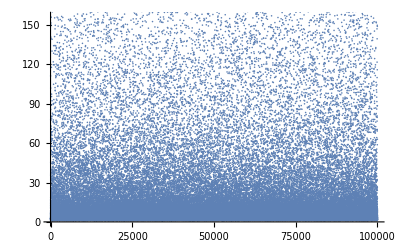

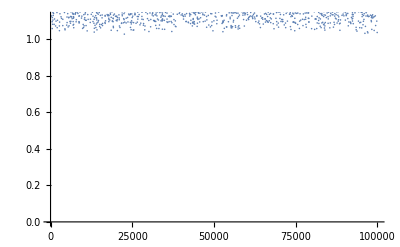

```mathematica
Clear[ϕ,ΔA,ΔB,AA,DD,AAT,AAH,AAC,DDT,DDH,α,β1,β2,β3,β4,β5,AαiA,d11,d12,d13,d21,d22,d23,d31,d32,d33,ψ11,ψ12,ψ13,ψ21,ψ22,ψ23,ψ31,ψ32,ψ33,Xαi,ψαi,dαi,M2,δ,λ,m,c,hbar,kb,u,m3,ms,Tc,vf,kf,Nf,c1,c2,c3,c4,c5,t,λbarList]
(*****************************************************************************)
(****************  introduce the 32bar strong coupling                  ******)
m=1;s=1;J=1;kg=1;k=1;
c=2.99792458 10^8 m s^-1;
hbar=1.054571817 10^-34 J s ;(* plank constant *)
kb=1.380649 10^-23 J k^-1;(**J.K^-1*)
(*π=3.1415926;*)
u= 1.66053906660 10^-27 kg ;
m3=3.016293 u;
(**pressure is 32 bar**)
ms=5.66 m3;
Tc=2.463 10^-3 k^-1;(*mK, kevin*)
vf=32.85 m s^-1;
kf=(vf ms)/hbar
Nf=(ms kf)/(2 π^2 hbar^2)
c1=-0.0402;c2 = -0.1583;c3=-0.0267;c4=-0.3388;c5=-0.3717;
(************************************)
(****** construct the M2, δ, λ ******)
λbarList={}; (*** saving list of λbar ***)
M2=2 (α-(2 (-1+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2) β1+2 d13^2 β3+(d21^2+d22^2+2 d23^2+d31^2+d32^2+2 d33^2) (β3+β4)+2 (d21^2+d22^2+d23^2+d31^2+d32^2+d33^2) β5-2 (β2+β3+β4+β5)) ΔA^2+2 d11^2 (β2+β4+β5) ΔA^2 Cos[ψ11]^2+4 d11 d12 (β2+β4+β5) ΔA^2 Cos[ψ11] Sin[ψ12]-ΔA^2 (-d21^2 β5 Cos[2 ψ21]+d22^2 β5 Cos[2 ψ22]-d31^2 β5 Cos[2 ψ31]+d32^2 β5 Cos[2 ψ32]-4 d11 d12 (β1+β3) Sin[ψ11-ψ12]-2 d12^2 (β2+β4+β5) Sin[ψ12]^2+2 d21 d22 ((-β3+β4) Sin[ψ21-ψ22]-β5 Sin[ψ21+ψ22])+2 d31 d32 ((-β3+β4) Sin[ψ31-ψ32]-β5 Sin[ψ31+ψ32])));
δ=6 √2 ΔA (-d11 d22^2 β1 Cos[ψ11-2 ψ22]-d12 d21 d22 (β5 Cos[ψ12-ψ21-ψ22]+β4 Cos[ψ12+ψ21-ψ22]+β3 Cos[ψ12-ψ21+ψ22])-d11 d23^2 β1 Cos[ψ11-2 ψ23]-d13 d21 d23 (β5 Cos[ψ13-ψ21-ψ23]+β4 Cos[ψ13+ψ21-ψ23]+β3 Cos[ψ13-ψ21+ψ23])-d11 d32^2 β1 Cos[ψ11-2 ψ32]-d12 d31 d32 (β5 Cos[ψ12-ψ31-ψ32]+β4 Cos[ψ12+ψ31-ψ32]+β3 Cos[ψ12-ψ31+ψ32])-d11 d33^2 β1 Cos[ψ11-2 ψ33]-d13 d31 d33 (β5 Cos[ψ13-ψ31-ψ33]+β4 Cos[ψ13+ψ31-ψ33]+β3 Cos[ψ13-ψ31+ψ33])+Cos[ψ11] (d11 ((-1+d22^2+d23^2+d32^2+d33^2) β1-β2+(-1+d22^2+d23^2+d32^2+d33^2) (β3+β4+β5))+2 d12^3 (β1+β3) Sin[ψ11-ψ12])-d12 (β1+β3) Sin[2 ψ11-ψ12]-d12 (β2+β4+β5) Sin[ψ12]-2 d11 d12^2 (β1+β3) Sin[ψ11-ψ12] Sin[ψ12]+2 d12 d13^2 (β1+β3) Cos[ψ11-ψ12+ψ13] Sin[ψ11-ψ13]-2 d11 d13^2 (β1+β3) Sin[ψ11-ψ13] Sin[ψ13]+d12 d21^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ21])-2 d11 d21^2 (β1+β5) Sin[ψ11-ψ21] Sin[ψ21]+d12 d22^2 ((β1+β3) Sin[2 ψ11-ψ12]+(-β3+β5) Sin[ψ12]+(β1+β5) Sin[ψ12-2 ψ22])+d11 d21 d22 (β5 Sin[ψ11-ψ21-ψ22]-β3 Sin[ψ11+ψ21-ψ22]-β4 Sin[ψ11-ψ21+ψ22])+d12 d23^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ23])+d13 d22 d23 (β5 Sin[ψ13-ψ22-ψ23]-β4 Sin[ψ13+ψ22-ψ23]-β3 Sin[ψ13-ψ22+ψ23])+d12 d31^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ31])-2 d11 d31^2 (β1+β5) Sin[ψ11-ψ31] Sin[ψ31]+d12 d32^2 ((β1+β3) Sin[2 ψ11-ψ12]+(-β3+β5) Sin[ψ12]+(β1+β5) Sin[ψ12-2 ψ32])+d11 d31 d32 (β5 Sin[ψ11-ψ31-ψ32]-β3 Sin[ψ11+ψ31-ψ32]-β4 Sin[ψ11-ψ31+ψ32])+d12 d33^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ33])+d13 d32 d33 (β5 Sin[ψ13-ψ32-ψ33]-β4 Sin[ψ13+ψ32-ψ33]-β3 Sin[ψ13-ψ32+ψ33]));
λ=4 (β2+2 d21^2 d31^2 β3+β4-2 d13^2 d21^2 β4-2 d22^2 β4-2 d23^2 β4-2 d13^2 d31^2 β4-2 d32^2 β4+2 d23^2 d32^2 β4-2 d33^2 β4+2 d22^2 d33^2 β4+2 d13^2 d23^2 (β3+β4)+2 d13^2 d33^2 (β3+β4)+2 d22^2 d32^2 (β3+2 β4)+2 d23^2 d33^2 (β3+2 β4)+d11^4 (β1+β3+β5)+d12^4 (β1+β3+β5)+d13^4 (β1+β3+β5)+d21^4 (β1+β3+β5)+d31^4 (β1+β3+β5)+2 d21^2 d22^2 (β4+β5)+2 d21^2 d23^2 (β4+β5)+2 d31^2 d32^2 (β4+β5)+2 d31^2 d33^2 (β4+β5)+2 d22^2 d23^2 (2 β4+β5)+2 d32^2 d33^2 (2 β4+β5)+d22^4 (β1+β3+2 β4+β5)+d23^4 (β1+β3+2 β4+β5)+d32^4 (β1+β3+2 β4+β5)+d33^4 (β1+β3+2 β4+β5)+2 d12^2 (-((d21^2+d31^2) β4)+d22^2 (β3+β4)+d32^2 (β3+β4)+d13^2 β5)+2 d11^2 ((d21^2+d31^2) β3+(d12^2+d13^2) β5)+2 (d11^2 d12^2 (β1+β3) Cos[2 ψ11-2 ψ12]+d11^2 d13^2 (β1+β3) Cos[2 ψ11-2 ψ13]+d12^2 d13^2 β1 Cos[2 ψ12-2 ψ13]+d12^2 d13^2 β3 Cos[2 ψ12-2 ψ13]+d11^2 d21^2 β1 Cos[2 ψ11-2 ψ21]+d11^2 d21^2 β5 Cos[2 ψ11-2 ψ21]+d12^2 d21^2 β1 Cos[2 ψ12-2 ψ21]+d13^2 d21^2 β1 Cos[2 ψ13-2 ψ21]+d11^2 d22^2 β1 Cos[2 ψ11-2 ψ22]+d12^2 d22^2 β1 Cos[2 ψ12-2 ψ22]+d12^2 d22^2 β5 Cos[2 ψ12-2 ψ22]+d13^2 d22^2 β1 Cos[2 ψ13-2 ψ22]+d21^2 d22^2 β1 Cos[2 ψ21-2 ψ22]+d21^2 d22^2 β3 Cos[2 ψ21-2 ψ22]+2 d11 d12 d21 d22 β5 Cos[ψ11+ψ12-ψ21-ψ22]+2 d11 d12 d21 d22 β3 Cos[ψ11-ψ12+ψ21-ψ22]+2 d11 d12 d21 d22 β4 Cos[ψ11-ψ12-ψ21+ψ22]+d11^2 d23^2 β1 Cos[2 ψ11-2 ψ23]+d12^2 d23^2 β1 Cos[2 ψ12-2 ψ23]+d13^2 d23^2 β1 Cos[2 ψ13-2 ψ23]+d13^2 d23^2 β5 Cos[2 ψ13-2 ψ23]+d21^2 d23^2 β1 Cos[2 ψ21-2 ψ23]+d21^2 d23^2 β3 Cos[2 ψ21-2 ψ23]+d22^2 d23^2 β1 Cos[2 ψ22-2 ψ23]+d22^2 d23^2 β3 Cos[2 ψ22-2 ψ23]+2 d11 d13 d21 d23 β5 Cos[ψ11+ψ13-ψ21-ψ23]+2 d11 d13 d21 d23 β3 Cos[ψ11-ψ13+ψ21-ψ23]+2 d12 d13 d22 d23 β5 Cos[ψ12+ψ13-ψ22-ψ23]+2 d12 d13 d22 d23 β3 Cos[ψ12-ψ13+ψ22-ψ23]+2 d11 d13 d21 d23 β4 Cos[ψ11-ψ13-ψ21+ψ23]+2 d12 d13 d22 d23 β4 Cos[ψ12-ψ13-ψ22+ψ23]+d11^2 d31^2 β1 Cos[2 ψ11-2 ψ31]+d11^2 d31^2 β5 Cos[2 ψ11-2 ψ31]+d12^2 d31^2 β1 Cos[2 ψ12-2 ψ31]+d13^2 d31^2 β1 Cos[2 ψ13-2 ψ31]+d21^2 d31^2 β1 Cos[2 ψ21-2 ψ31]+d21^2 d31^2 β5 Cos[2 ψ21-2 ψ31]+d22^2 d31^2 β1 Cos[2 ψ22-2 ψ31]+d23^2 d31^2 β1 Cos[2 ψ23-2 ψ31]+d11^2 d32^2 β1 Cos[2 ψ11-2 ψ32]+d12^2 d32^2 β1 Cos[2 ψ12-2 ψ32]+d12^2 d32^2 β5 Cos[2 ψ12-2 ψ32]+d13^2 d32^2 β1 Cos[2 ψ13-2 ψ32]+d21^2 d32^2 β1 Cos[2 ψ21-2 ψ32]+d22^2 d32^2 β1 Cos[2 ψ22-2 ψ32]+d22^2 d32^2 β5 Cos[2 ψ22-2 ψ32]+d23^2 d32^2 β1 Cos[2 ψ23-2 ψ32]+d31^2 d32^2 β1 Cos[2 ψ31-2 ψ32]+d31^2 d32^2 β3 Cos[2 ψ31-2 ψ32]+2 d11 d12 d31 d32 β5 Cos[ψ11+ψ12-ψ31-ψ32]+2 d21 d22 d31 d32 β5 Cos[ψ21+ψ22-ψ31-ψ32]+2 d11 d12 d31 d32 β3 Cos[ψ11-ψ12+ψ31-ψ32]+2 d21 d22 d31 d32 β3 Cos[ψ21-ψ22+ψ31-ψ32]+2 d11 d12 d31 d32 β4 Cos[ψ11-ψ12-ψ31+ψ32]+2 d21 d22 d31 d32 β4 Cos[ψ21-ψ22-ψ31+ψ32]+d11^2 d33^2 β1 Cos[2 ψ11-2 ψ33]+d12^2 d33^2 β1 Cos[2 ψ12-2 ψ33]+d13^2 d33^2 β1 Cos[2 ψ13-2 ψ33]+d13^2 d33^2 β5 Cos[2 ψ13-2 ψ33]+d21^2 d33^2 β1 Cos[2 ψ21-2 ψ33]+d22^2 d33^2 β1 Cos[2 ψ22-2 ψ33]+d23^2 d33^2 β1 Cos[2 ψ23-2 ψ33]+d23^2 d33^2 β5 Cos[2 ψ23-2 ψ33]+d31^2 d33^2 β1 Cos[2 ψ31-2 ψ33]+d31^2 d33^2 β3 Cos[2 ψ31-2 ψ33]+d32^2 d33^2 β1 Cos[2 ψ32-2 ψ33]+d32^2 d33^2 β3 Cos[2 ψ32-2 ψ33]+2 d11 d13 d31 d33 β5 Cos[ψ11+ψ13-ψ31-ψ33]+2 d21 d23 d31 d33 β5 Cos[ψ21+ψ23-ψ31-ψ33]+2 d11 d13 d31 d33 β3 Cos[ψ11-ψ13+ψ31-ψ33]+2 d21 d23 d31 d33 β3 Cos[ψ21-ψ23+ψ31-ψ33]+2 d12 d13 d32 d33 β5 Cos[ψ12+ψ13-ψ32-ψ33]+2 d22 d23 d32 d33 β5 Cos[ψ22+ψ23-ψ32-ψ33]+2 d12 d13 d32 d33 β3 Cos[ψ12-ψ13+ψ32-ψ33]+2 d22 d23 d32 d33 β3 Cos[ψ22-ψ23+ψ32-ψ33]+2 d11 d13 d31 d33 β4 Cos[ψ11-ψ13-ψ31+ψ33]+2 d21 d23 d31 d33 β4 Cos[ψ21-ψ23-ψ31+ψ33]+2 d12 d13 d32 d33 β4 Cos[ψ12-ψ13-ψ32+ψ33]+2 d22 d23 d32 d33 β4 Cos[ψ22-ψ23-ψ32+ψ33]));
(***************************************)
(**************  All βi ****************)
t=0.;
βwc1=-(7 Nf Zeta[3])/(240 π^2 kb^2 Tc^2);
βwc2=-2 βwc1;βwc3=-2 βwc1;βwc4=-2 βwc1;βwc5=2 βwc1;
βsc1=c1 Abs[βwc1];βsc2=c2 Abs[βwc1];
βsc3=c3 Abs[βwc1];
βsc4=c4 Abs[βwc1];
βsc5=c5 Abs[βwc1];
β1=βwc1+t βsc1;β2=βwc2+t βsc2;
β3=βwc3+t βsc3;
β4=βwc4+t βsc4;
β5=βwc5+t βsc5;
(***** Gap of A and B - phase *****)
α=1/3 Nf (t-1);
βA=β2+β4+β5;
βB=β1+β2+1/3 (β3+β4+β5);
ΔA=√(-α/(2 βA))
(****************************************************)
(***************** generate dαi *********************)
n=1;
While[n<=100000,
Xαi=RandomReal[1,9]; (* 9 uniformly distributed real numbers in [0,1]*)
NormalizedCoefficient=√Sum[i^2,{i,Xαi}];
dαi=1/NormalizedCoefficient Xαi;
(***************************)
(****** generate ψαi *******)
(*Print[Style[" random list of ψαi: ",18,Red]];*)
Xαi=RandomReal[1,9]; (* 9 uniformly distributed real numbers in [0,1]*)
ψαi=4 π Xαi;
(************************************)
(******** assigen the elemtes *******)
d11=dαi[[1]];d12=dαi[[2]];d13=dαi[[3]];d21=dαi[[4]];
d22=dαi[[5]];d23=dαi[[6]];d31=dαi[[7]];d32=dαi[[8]];d33=dαi[[9]];
ψ11=ψαi[[1]];ψ12=ψαi[[2]];ψ13=ψαi[[3]];ψ21=ψαi[[4]];
ψ22=ψαi[[5]];ψ23=ψαi[[6]];ψ31=ψαi[[7]];ψ32=dαi[[8]];ψ33=ψαi[[9]];
(************************************)
(************ save the λbar *********)
AppendTo[λbarList,9/2 M2/δ^2 λ];
(*Print[Style[" loop now is: ",18,Blue],n,Style[" λbar is :",18,Blue],9/2 M2/δ^2 λ];*)
n++];
(*************************************)
(*** scattering plot the λbarList ****)
ListPlot[λbarList]
ListPlot[λbarList,PlotRange->1.125]
```

```mathematica
N[9/8]
```

1.125

```mathematica
Clear[ΔA,ΔB,ϕ0,Dαi,t]
M2=2 (α-(2 (-1+d13^2+d21^2+d22^2+d23^2+d31^2+d32^2+d33^2) β1+2 d13^2 β3+(d21^2+d22^2+2 d23^2+d31^2+d32^2+2 d33^2) (β3+β4)+2 (d21^2+d22^2+d23^2+d31^2+d32^2+d33^2) β5-2 (β2+β3+β4+β5)) ΔA^2+2 d11^2 (β2+β4+β5) ΔA^2 Cos[ψ11]^2+4 d11 d12 (β2+β4+β5) ΔA^2 Cos[ψ11] Sin[ψ12]-ΔA^2 (-d21^2 β5 Cos[2 ψ21]+d22^2 β5 Cos[2 ψ22]-d31^2 β5 Cos[2 ψ31]+d32^2 β5 Cos[2 ψ32]-4 d11 d12 (β1+β3) Sin[ψ11-ψ12]-2 d12^2 (β2+β4+β5) Sin[ψ12]^2+2 d21 d22 ((-β3+β4) Sin[ψ21-ψ22]-β5 Sin[ψ21+ψ22])+2 d31 d32 ((-β3+β4) Sin[ψ31-ψ32]-β5 Sin[ψ31+ψ32])));
δ=6 √2 ΔA (-d11 d22^2 β1 Cos[ψ11-2 ψ22]-d12 d21 d22 (β5 Cos[ψ12-ψ21-ψ22]+β4 Cos[ψ12+ψ21-ψ22]+β3 Cos[ψ12-ψ21+ψ22])-d11 d23^2 β1 Cos[ψ11-2 ψ23]-d13 d21 d23 (β5 Cos[ψ13-ψ21-ψ23]+β4 Cos[ψ13+ψ21-ψ23]+β3 Cos[ψ13-ψ21+ψ23])-d11 d32^2 β1 Cos[ψ11-2 ψ32]-d12 d31 d32 (β5 Cos[ψ12-ψ31-ψ32]+β4 Cos[ψ12+ψ31-ψ32]+β3 Cos[ψ12-ψ31+ψ32])-d11 d33^2 β1 Cos[ψ11-2 ψ33]-d13 d31 d33 (β5 Cos[ψ13-ψ31-ψ33]+β4 Cos[ψ13+ψ31-ψ33]+β3 Cos[ψ13-ψ31+ψ33])+Cos[ψ11] (d11 ((-1+d22^2+d23^2+d32^2+d33^2) β1-β2+(-1+d22^2+d23^2+d32^2+d33^2) (β3+β4+β5))+2 d12^3 (β1+β3) Sin[ψ11-ψ12])-d12 (β1+β3) Sin[2 ψ11-ψ12]-d12 (β2+β4+β5) Sin[ψ12]-2 d11 d12^2 (β1+β3) Sin[ψ11-ψ12] Sin[ψ12]+2 d12 d13^2 (β1+β3) Cos[ψ11-ψ12+ψ13] Sin[ψ11-ψ13]-2 d11 d13^2 (β1+β3) Sin[ψ11-ψ13] Sin[ψ13]+d12 d21^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ21])-2 d11 d21^2 (β1+β5) Sin[ψ11-ψ21] Sin[ψ21]+d12 d22^2 ((β1+β3) Sin[2 ψ11-ψ12]+(-β3+β5) Sin[ψ12]+(β1+β5) Sin[ψ12-2 ψ22])+d11 d21 d22 (β5 Sin[ψ11-ψ21-ψ22]-β3 Sin[ψ11+ψ21-ψ22]-β4 Sin[ψ11-ψ21+ψ22])+d12 d23^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ23])+d13 d22 d23 (β5 Sin[ψ13-ψ22-ψ23]-β4 Sin[ψ13+ψ22-ψ23]-β3 Sin[ψ13-ψ22+ψ23])+d12 d31^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ31])-2 d11 d31^2 (β1+β5) Sin[ψ11-ψ31] Sin[ψ31]+d12 d32^2 ((β1+β3) Sin[2 ψ11-ψ12]+(-β3+β5) Sin[ψ12]+(β1+β5) Sin[ψ12-2 ψ32])+d11 d31 d32 (β5 Sin[ψ11-ψ31-ψ32]-β3 Sin[ψ11+ψ31-ψ32]-β4 Sin[ψ11-ψ31+ψ32])+d12 d33^2 ((β1+β3) Sin[2 ψ11-ψ12]+(β4+β5) Sin[ψ12]+β1 Sin[ψ12-2 ψ33])+d13 d32 d33 (β5 Sin[ψ13-ψ32-ψ33]-β4 Sin[ψ13+ψ32-ψ33]-β3 Sin[ψ13-ψ32+ψ33]));
λ=4 (β2+2 d21^2 d31^2 β3+β4-2 d13^2 d21^2 β4-2 d22^2 β4-2 d23^2 β4-2 d13^2 d31^2 β4-2 d32^2 β4+2 d23^2 d32^2 β4-2 d33^2 β4+2 d22^2 d33^2 β4+2 d13^2 d23^2 (β3+β4)+2 d13^2 d33^2 (β3+β4)+2 d22^2 d32^2 (β3+2 β4)+2 d23^2 d33^2 (β3+2 β4)+d11^4 (β1+β3+β5)+d12^4 (β1+β3+β5)+d13^4 (β1+β3+β5)+d21^4 (β1+β3+β5)+d31^4 (β1+β3+β5)+2 d21^2 d22^2 (β4+β5)+2 d21^2 d23^2 (β4+β5)+2 d31^2 d32^2 (β4+β5)+2 d31^2 d33^2 (β4+β5)+2 d22^2 d23^2 (2 β4+β5)+2 d32^2 d33^2 (2 β4+β5)+d22^4 (β1+β3+2 β4+β5)+d23^4 (β1+β3+2 β4+β5)+d32^4 (β1+β3+2 β4+β5)+d33^4 (β1+β3+2 β4+β5)+2 d12^2 (-((d21^2+d31^2) β4)+d22^2 (β3+β4)+d32^2 (β3+β4)+d13^2 β5)+2 d11^2 ((d21^2+d31^2) β3+(d12^2+d13^2) β5)+2 (d11^2 d12^2 (β1+β3) Cos[2 ψ11-2 ψ12]+d11^2 d13^2 (β1+β3) Cos[2 ψ11-2 ψ13]+d12^2 d13^2 β1 Cos[2 ψ12-2 ψ13]+d12^2 d13^2 β3 Cos[2 ψ12-2 ψ13]+d11^2 d21^2 β1 Cos[2 ψ11-2 ψ21]+d11^2 d21^2 β5 Cos[2 ψ11-2 ψ21]+d12^2 d21^2 β1 Cos[2 ψ12-2 ψ21]+d13^2 d21^2 β1 Cos[2 ψ13-2 ψ21]+d11^2 d22^2 β1 Cos[2 ψ11-2 ψ22]+d12^2 d22^2 β1 Cos[2 ψ12-2 ψ22]+d12^2 d22^2 β5 Cos[2 ψ12-2 ψ22]+d13^2 d22^2 β1 Cos[2 ψ13-2 ψ22]+d21^2 d22^2 β1 Cos[2 ψ21-2 ψ22]+d21^2 d22^2 β3 Cos[2 ψ21-2 ψ22]+2 d11 d12 d21 d22 β5 Cos[ψ11+ψ12-ψ21-ψ22]+2 d11 d12 d21 d22 β3 Cos[ψ11-ψ12+ψ21-ψ22]+2 d11 d12 d21 d22 β4 Cos[ψ11-ψ12-ψ21+ψ22]+d11^2 d23^2 β1 Cos[2 ψ11-2 ψ23]+d12^2 d23^2 β1 Cos[2 ψ12-2 ψ23]+d13^2 d23^2 β1 Cos[2 ψ13-2 ψ23]+d13^2 d23^2 β5 Cos[2 ψ13-2 ψ23]+d21^2 d23^2 β1 Cos[2 ψ21-2 ψ23]+d21^2 d23^2 β3 Cos[2 ψ21-2 ψ23]+d22^2 d23^2 β1 Cos[2 ψ22-2 ψ23]+d22^2 d23^2 β3 Cos[2 ψ22-2 ψ23]+2 d11 d13 d21 d23 β5 Cos[ψ11+ψ13-ψ21-ψ23]+2 d11 d13 d21 d23 β3 Cos[ψ11-ψ13+ψ21-ψ23]+2 d12 d13 d22 d23 β5 Cos[ψ12+ψ13-ψ22-ψ23]+2 d12 d13 d22 d23 β3 Cos[ψ12-ψ13+ψ22-ψ23]+2 d11 d13 d21 d23 β4 Cos[ψ11-ψ13-ψ21+ψ23]+2 d12 d13 d22 d23 β4 Cos[ψ12-ψ13-ψ22+ψ23]+d11^2 d31^2 β1 Cos[2 ψ11-2 ψ31]+d11^2 d31^2 β5 Cos[2 ψ11-2 ψ31]+d12^2 d31^2 β1 Cos[2 ψ12-2 ψ31]+d13^2 d31^2 β1 Cos[2 ψ13-2 ψ31]+d21^2 d31^2 β1 Cos[2 ψ21-2 ψ31]+d21^2 d31^2 β5 Cos[2 ψ21-2 ψ31]+d22^2 d31^2 β1 Cos[2 ψ22-2 ψ31]+d23^2 d31^2 β1 Cos[2 ψ23-2 ψ31]+d11^2 d32^2 β1 Cos[2 ψ11-2 ψ32]+d12^2 d32^2 β1 Cos[2 ψ12-2 ψ32]+d12^2 d32^2 β5 Cos[2 ψ12-2 ψ32]+d13^2 d32^2 β1 Cos[2 ψ13-2 ψ32]+d21^2 d32^2 β1 Cos[2 ψ21-2 ψ32]+d22^2 d32^2 β1 Cos[2 ψ22-2 ψ32]+d22^2 d32^2 β5 Cos[2 ψ22-2 ψ32]+d23^2 d32^2 β1 Cos[2 ψ23-2 ψ32]+d31^2 d32^2 β1 Cos[2 ψ31-2 ψ32]+d31^2 d32^2 β3 Cos[2 ψ31-2 ψ32]+2 d11 d12 d31 d32 β5 Cos[ψ11+ψ12-ψ31-ψ32]+2 d21 d22 d31 d32 β5 Cos[ψ21+ψ22-ψ31-ψ32]+2 d11 d12 d31 d32 β3 Cos[ψ11-ψ12+ψ31-ψ32]+2 d21 d22 d31 d32 β3 Cos[ψ21-ψ22+ψ31-ψ32]+2 d11 d12 d31 d32 β4 Cos[ψ11-ψ12-ψ31+ψ32]+2 d21 d22 d31 d32 β4 Cos[ψ21-ψ22-ψ31+ψ32]+d11^2 d33^2 β1 Cos[2 ψ11-2 ψ33]+d12^2 d33^2 β1 Cos[2 ψ12-2 ψ33]+d13^2 d33^2 β1 Cos[2 ψ13-2 ψ33]+d13^2 d33^2 β5 Cos[2 ψ13-2 ψ33]+d21^2 d33^2 β1 Cos[2 ψ21-2 ψ33]+d22^2 d33^2 β1 Cos[2 ψ22-2 ψ33]+d23^2 d33^2 β1 Cos[2 ψ23-2 ψ33]+d23^2 d33^2 β5 Cos[2 ψ23-2 ψ33]+d31^2 d33^2 β1 Cos[2 ψ31-2 ψ33]+d31^2 d33^2 β3 Cos[2 ψ31-2 ψ33]+d32^2 d33^2 β1 Cos[2 ψ32-2 ψ33]+d32^2 d33^2 β3 Cos[2 ψ32-2 ψ33]+2 d11 d13 d31 d33 β5 Cos[ψ11+ψ13-ψ31-ψ33]+2 d21 d23 d31 d33 β5 Cos[ψ21+ψ23-ψ31-ψ33]+2 d11 d13 d31 d33 β3 Cos[ψ11-ψ13+ψ31-ψ33]+2 d21 d23 d31 d33 β3 Cos[ψ21-ψ23+ψ31-ψ33]+2 d12 d13 d32 d33 β5 Cos[ψ12+ψ13-ψ32-ψ33]+2 d22 d23 d32 d33 β5 Cos[ψ22+ψ23-ψ32-ψ33]+2 d12 d13 d32 d33 β3 Cos[ψ12-ψ13+ψ32-ψ33]+2 d22 d23 d32 d33 β3 Cos[ψ22-ψ23+ψ32-ψ33]+2 d11 d13 d31 d33 β4 Cos[ψ11-ψ13-ψ31+ψ33]+2 d21 d23 d31 d33 β4 Cos[ψ21-ψ23-ψ31+ψ33]+2 d12 d13 d32 d33 β4 Cos[ψ12-ψ13-ψ32+ψ33]+2 d22 d23 d32 d33 β4 Cos[ψ22-ψ23-ψ32+ψ33]));
(*********************)
t=0.4;
βwc1=-(7 Nf Zeta[3])/(240 π^2 kb^2 Tc^2);
βwc2=-2 βwc1;βwc3=-2 βwc1;βwc4=-2 βwc1;βwc5=2 βwc1;
βsc1=c1 Abs[βwc1];βsc2=c2 Abs[βwc1];
βsc3=c3 Abs[βwc1];
βsc4=c4 Abs[βwc1];
βsc5=c5 Abs[βwc1];
β1=βwc1+t βsc1;β2=βwc2+t βsc2;
β3=βwc3+t βsc3;
β4=βwc4+t βsc4;
β5=βwc5+t βsc5;
(***** Gap of A and B - phase *****)
α=1/3 Nf (t-1);
βA=β2+β4+β5;
βB=β1+β2+1/3 (β3+β4+β5);
ΔA=√(-α/(2 βA))
ΔB=√(-α/(2 βB))
ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)
Dαi=N[1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}](* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Dαi//MatrixForm
(*******************************)
d11=0.08845517415055668;d12=0.6325435552450193;d13=0.0;d21=0.0;
d22=0.5440883810944626;d23=0.0;d31=0.0;d32=0.0;d33=0.5440883810944626;
ψ11=π;ψ12=3/2 π;ψ13=5.0;ψ21=0.0;
ψ22=0.0;ψ23=0.0;ψ31=0.0;ψ32=0.0;ψ33=0.0;
9/2 M2/δ^2 λ
```

1.40354×10^-25

1.47859×10^-25

1.56898×10^-25

{{-0.0884552,0.-0.632544 ⅈ,0.},{0.,0.544088,0.},{0.,0.,0.544088}}

(-0.0884552 | 0.-0.632544 ⅈ | 0.
0. | 0.544088 | 0.
0. | 0. | 0.544088)

0.876829